## ECO6108 Han Sun 6986498 Assignment 2

1.  In this exercise, we analyze a simplified q model. Suppose that a firm faces a market interest rate r and has the following production function in year t: Y_t=A_t F[K_t], where A_t is a productivity parameter; K_t is its capital stock; and Y_t is the output -- all in year t, t = 0, 1,... Here we treat the labor input as fixed because we want to concentrate on the investment decisions of the firm. The objective of the firm is to maximize the present value of profits. The exercise deals with the real-life problem that capital cannot be installed, or dismantled and moved into a different line of work, without incurring frictional costs, and these costs will be typically higher the more dramatic is the capital-stock change: management becomes spread more thinly, and there is greater disruption to current production, and so forth. 

Suppose that if I_t is the investment or disinvestment made in year t, then the adjustment cost is 1/2 χ I_t^2, where χ > 0 is a constant. The profit in year t is thus given by A_t F[K_t]-I_t-1/2 χ I_t^2, and the capital stock in the following year is K_(t+1)=K_t+I_t. The problem that the firm must solve is to find an investment program (I_t)_(t=0)^∞ to maximize the following discounted profit:

(1)	∑_(t=0)^∞ 1/(1+r)^t(A_t F[K_t]-I_t-1/2 χI_t^2) 

subject to the capital accumulation constraint

(2)	K_(t+1)=K_t+I_t, K_0 is given.

For each t = 0, 1,..., let 

(3)	v_t[K_t]=max_((I_s)_(s=t)^∞) ∑_(s=t)^∞ 1/(1+r)^(s-t)(A_s F[K_s]-I_s-1/2 χ I_s^2) 

subject to 

(4)	K_(s+1)=K_s+I_s, K_t is given. 

As defined, v[K_t] gives the optimal discounted profits -- discounted back to year t -- given that the firm begins in year t with K_t as its capital stock. The function v_t[K_t] is known as the optimal-value function or the Bellman function of the firm. 

Let (I_t^*)_(t=0)^∞ be the solution of the problem of maximizing (1) subject to (2), and K_t^* be the capital stock in year t under the optimal investment program, i.e.,

(5)	K_(t+1)^*=K_t^*+I_t^*, K_t^*=K_0  for t=0.

(a) Let q_t=v'_t[K_t^*] be the shadow price of capital (or the Tobin's q) in period t along the optimal trajectory. Find the difference equations that link (q_(t+1),K_(t+1)^*)  to  (q_t^*,K_t^*). Assume that the productivity parameter is constant over time, say A_t=A=constant. Draw a phase diagram with K on the horizontal axis and q on the vertical axis, then explain how the system converges to the steady state. 

(b) Suppose that the system is in steady state. Suddenly, there is an unanticipated permanent increase in A. Show the new steady state and the transition to the new steady state.

#### Answer to question (a)

(a) Suppose that the firm begins at time t with K_t as its stock of capital. It has to find an investment program (I_s)_(s=t)^∞ to maximize discounted profits. Formally, it solves the following maximization problem:
(1)	v_t[K_t]=max_((I_s)_(s=t)^∞) (∑_(s=t)^∞ (1/(1+r))^(s-t)(A_s F[K_s]-I_s-1/2 χ I_s^2))
	subject to K_(s+1)=K_s+I_s,s=t,t+1,...,K_t is given.

To solve the above problem, we use dynamic programming. Applying the principle of optimality to (1), we obtain the following Bellman equation:

(2)	v_t[K_t]=max_I_t (A_t F[K_t]-I_t-1/2 χ I_t^2+1/(1+r)v_(t+1)[K_t+I_t]).

The optimal investment in period t satisfies the following first-order condition
(3)	-1-χ I_t+1/(1+r)v'_(t+1)[K_t+I_t]=0⟹I_t=(-1+1/(1+r)v'_(t+1)[K_t+I_t])/χ.

Applying the envelope theorem in period t, we obtain
(4)	v'_t[K_t]=A_t F'[K_t]+1/(1+r)v'_(t+1)[K_t+I_t].

Now let q_t=v'_t[K_t],q_(t+1)=v'_(t+1)[K_(t+1)],... We can then rewrite (3) and (4), respectively, as follows:

(5)	I_t=(-1+1/(1+r)q_(t+1))/χ,
(6)	q_t=A_t F'[K_t]+1/(1+r)q_(t+1).

Using (5), we obtain the following difference equation that describes the dynamics of capital accumulation:
(7)	K_(s+1)-K_s=(-1+1/(1+r)q_(s+1))/χ,s≥ t.

The dynamics of the current shadow price of capital, namely (6), can be rewritten as follows:
(8)	q_(s+1)-q_s=r q_s-(1+r)A_s F'[K_s],s≥ t.

Suppose now that A_t=A_(t+1)=...=A=constant. Then the stationary equilibrium of the system can be found by setting K_(s+1)=K_s=K̄ and q_(s+1)=q_s=q̄ in (7) and (8). The results are

(9)	q̄=1+r,A F'[K̄]=r. 

The system of difference equations (7) and (8) can be analyzed with the help of a phase diagram as follows. To draw the phase diagram by Mathematica, we need to assume a functional form for the production technology, say F[K]=K^α,0<α<1.

```mathematica
F[K_]:=K^α
```

```mathematica
F[K]
```

K^α

```mathematica
F'[K]
```

K^(-1+α) α

The preliminary calculations are carried out by Mathematica to compute the stationary equilibrium (K̄,q̄). Using (9), we can write

```mathematica
qBar=1+r
```

1+r

```mathematica
s[0]=Solve[A F'[K]==r,K]//Flatten
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{K→(r/(A α))^(1/(-1+α))}

```mathematica
KBar=K/.s[0]
```

(r/(A α))^(1/(-1+α))

The motion of the stock of capital is governed by equation (7), namely

```mathematica
eq[1]=K[s+1]-K[s]==(-1+1/(1+r) q[s+1])/χ
```

-K[s]+K[1+s]==(-1+q[1+s]/(1+r))/χ

The motion of the shadow price of capital is governed by equation (8), namely

```mathematica
eq[2]=q[s+1]-q[s]==r q[s]-(1+r)  A F'[K]/.K-> K[s]
```

-q[s]+q[1+s]==-A (1+r) α K[s]^(-1+α)+r q[s]

Solving eq[ 1] and eq[2] for K_(s+1) and q_(s+1), we obtain

```mathematica
s[1]=Solve[{eq[1],eq[2]},{K[s+1],q[s+1]}]//Flatten
```

{K[1+s]→(-K[s]+χ K[s]^2-A α K[s]^α+K[s] q[s])/(χ K[s]),q[1+s]→((1+r) (-A α K[s]^α+K[s] q[s]))/K[s]}

```mathematica
s[1]=s[1]//FullSimplify
```

{K[1+s]→(-1+χ K[s]-A α K[s]^(-1+α)+q[s])/χ,q[1+s]→(1+r) (-A α K[s]^(-1+α)+q[s])}

The expression for K_(s+1) is

(10)	K_(s+1)=(-1+χ K_s-A α K_s^(-1+α)+q_s)/χ= (-1-A α K_s^(-1+α)+q_s)/χ+K_s ,

which implies that K_(s+1)-K_s>0 if (-1-A α K_s^(-1+α)+q_s)/χ>0 or if

(11)	q_s>1+A K_s^(α-1) α.

Thus if (K_s,q_s) is above the curve 
(12)	q=1+A K^(α-1) α, 
then K_(s+1)>K_s. If (K_s,q_s) is below the curve q=1+A K^(α-1) α, then K_(s+1)<K_s. If (K_s,q_s) is on the curve q=1+A K^(α-1) α, then K_(s+1)=K_s.

The expression for q_(s+1)is 
(13)	q_(1+s)=(1+r) (-A α K_s^(-1+α)+q_s)
	
which implies that q_(s+1)-q_s>0 if 
(14)	q_s>(1+r)/r A K_s^(α-1) α. 

Thus if (K_s,q_s) is above the curve 
(15)	q=(1+r)/r A K^(α-1) α, 
then q_(s+1)>q_s. If (K_s,q_s) is below the curve q=(1+r)/r A K^(α-1) α, then q_(s+1)<q_s. If (K_s,q_s) is  on the curve q=(1+r)/r A K^(α-1) α, then q_(s+1)=q_s.

The curve along which the stock of capital remains the same from one period to the next is (12), which can be represented in Mathematica as follows

```mathematica
dK=1+A K^(α-1) α
```

1+A K^(-1+α) α

The curve along which the shadow price of capital remains the same from one period to the next is (15), which can be represented in Mathematica as follows

```mathematica
dq=(1+r)/r A K^(α-1) α
```

(A K^(-1+α) (1+r) α)/r

The following figure depicts the phase diagram for the problem.

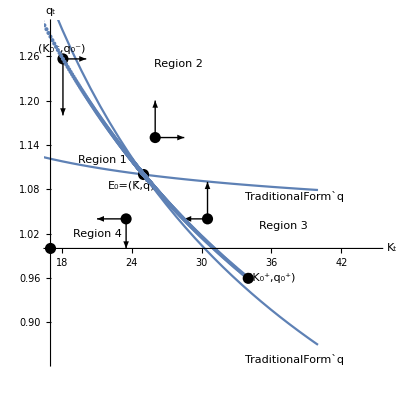
-Graphics-
Figure 1._ The Phase Diagram for Question (a)

In the phase diagram, the curve
(12)	q=1+A K^(α-1) α, K>0,
is strictly decreasing. It approaches asymptotically the horizontal line with vertical co-ordinate equal to 1 when K→ ∞. When K→ 0, this curve approaches the vertical axis asymptotically.

As for the curve
(15)	q=(1+r)/r A K^(α-1) α, 
it approaches asymptotically the horizontal axis when K→ ∞. When K→ 0, this curve approaches the vertical axis asymptotically.

Now the ratio
(16)	(1+A K^(α-1) α,)/((1+r)/r A K^(α-1) α)=r/((1+r)A K^(α-1) α)+r/(1+r)
is strictly increasing in K. Furthermore, it tends to r/(1+r)<1 when K→ 0, and tends to infinity when K→ ∞. Thus, the the curves (12) is above the curve (15) when K is small and dips below the curve (15) when K is large, with the ensuing consequence that they cross each other at a single point, which is the long-run equilibrium of the system E=(K̄,q̄), as depicted in the phase diagram.

The curves (12) and (15) partition the first quadrant of the plane into 4 regions.

(i) Region 1 consists of all the points (K,q) that are below the curve (15) and above the curve (12). At a point, say (K_t,q_t), we have K_(t+1)>K_t and q_(t+1)<q_t, and the arrows show the evolution of the system through time: the firm accumulates capital and the shadow price of capital falls as the stock of capital rises.

(ii) Region 2 consistes of all the points on or above the two curves (12) and (15). In this region, the capital stock and the shadow price of capital both rise through time without bounds. According to (5), the investment in period t tends to infinity when q_(t+1)→ ∞. That is, if the system ever enters Region 2, the two difference equations (6) and (7) which govern the motion of the system will drive both K_t and q_t to infinity. Now consider a period t when both K_t and q_(t+1) are very larege. Because q_(t+1) is large, I_t^* must also be very large according to (5). The cost of investment in period t is I_t^*+1/2 χ (I_t^*)^2>I_t^*. On the other hand, the extra output in period t+1 due to the investment I_t^* is A F[K_(t+1)^*]-A F[K_t^*]<A F'[K_t^*] I_t^* due to the concavity of A F[K]. Thus, the gain in discounted profit due to the investment I_t^* is
	1/(1+r)(A F[K_(t+1)^*]-A F[K_t^*])-I_t^*-1/2 χ (I_t^*)^2<1/(1+r)A F'[K_t^*] I_t^*-I_t^*-1/2 χ (I_t^*)^2
	=I_t^* (1/(1+r)A F'[K_t^*] -1-1/2 χ I_t^*)<0.

Note that the strict inequality follows from the assumption that A F'[K]→ 0 when K→ ∞, and this inequality means that the investment I_t^* leads to a decrease in the discounted profit, contradicting the optimality of I_t^*. Thus, under the optimal investment program, the system never enters Region 2.

(iii) Region 3 consists of all the points (K,q) that are below the curve (12) and above the curve (15). At a point, say (K_t,q_t), we have K_(t+1)<K_t and q_(t+1)>q_t, and the arrows show the evolution of the system through time: the firm decumulates capital and the shadow price of capital rises as the stock of capital declines.

(iv) Region 4 consists of all the points (K,q) that are on or below the curve (12) and on or below the curve (15). At a point, say (K_t,q_t), we have K_(t+1)<K_t and q_(t+1)<q_t, and the arrows show the evolution of the system through time: the firm decumulates capital and the shadow price of capital falls as the stock of capital declines. In finite time, either K_t or q_t will become negative. That q_t becomes negative is not possible because the shadow price of capital cannot be negative. As for K_t becoming negative, the system becomes incoherent. Thus, if we presume that the investment problem has a solution, the system cannot enter Region 4.

To describe the convergence of the system to its long-run equilibrium, we first consider the case the initial capital stock is below its long-run level, say K_0^-<K̄. Let q_0^- denote the initial shadow price of capital. With K_0^-<K̄, we must have (K_0^-,q_0^_) belonging to Region 1 (it cannot belong to Region 4), and the system converges to the long-run equilibrium along the curve (K_0^-,q_(0^-))E_0.

Next, consider the case the initial capital stock is above its long-run level, say K_0^+>K̄. Let q_0^+ denote the initial shadow price of capital. With K_0^->K̄, we must have (K_0^+,q_0^+) belonging to Region 3 (it cannot belong to Region 2), and the system converges to the long-run equilibrium along the curve (K_0^+,q_0^+)E_0.

#### Answer to question (b)

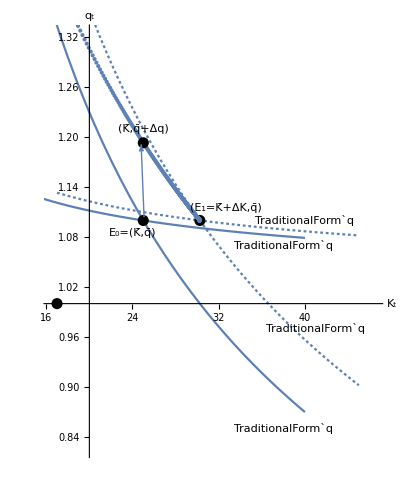
(b) Suppose that the system is in steady state, i.e., the system is in state E_0=(K̄,q̄). Suddenly, there is an unanticipated rise in the total factor productivity from A to A+ΔA. If we choose the current period as period 0, the problem faced by the firm is now

(17)	v_0[K̄]=max_((I_t)_(t=0)^∞) ∑_(t=0)^∞ (A+ΔA)F[K_t]-I_t-1/2 χ I_t^2) 

subject to 

(18)	K_(t+1)=K_t+I_t, K_0=K̄.

The solution of the problem constituted by (17) and (18) can be obtained by carrying out the same analysis as in (a), but with A+ΔA in place of A. Figure 2 depicts the phase diagram for the case of unanticipated rise in productivity from A to A+ΔA.

-Graphics-
Figure 2._ The Phase Diagram for the Case of an Unanticipated Rise in Productivity A→ A+ΔA

Note that because ΔA>0, the curve q=1+(A+ΔA)K^(α-)α is above the curve q=1+A K^(α-1)α. That is, the former curve is obtained by shifting the latter curve vertically upward. Similarly, the curve q=(1+r)/r(A+ΔA) K^(α-1)α is obtained by shifting the curve q=(1+r)/r A K^(α-1)α upward. Nets, note that because A+ΔA>A, the ratio
	(1+(A+ΔA) K^(α-1)α)/((1+r)/r(A+ΔA)K^(α-1)α)=r/(1+r)1/((A+ΔA)K^(α-1)α)+r/(1+r)<r/(1+r)1/(AK^(α-1)α)+r/(1+r),
and this means at K=K̄, we have
	(1+(A+ΔA) (K̄)^(α-1)α)/((1+r)/r(A+ΔA)(K̄)^(α-1)α)=r/(1+r)1/((A+ΔA)(K̄)^(α-1)α)+r/(1+r)<r/(1+r)1/(A (K̄)^(α-1)α)+r/(1+r)=1.
The inequality 
	(1+(A+ΔA) (K̄)^(α-1)α)/((1+r)/r(A+ΔA)(K̄)^(α-1)α)<1
means that the curve q=1+(A+ΔA)K^(α-)α is below the curve q=1+A K^(α-1)α at K=K̄. Thus the two curves q=1+(A+ΔA)K^(α-)α and q=(1+r)/r(A+ΔA) K^(α-1)α must cross each other at a point E_1 on the right-hand side of the vertical line with horizontal coordinate K̄. That is, the new long-run equilibrium E_1 is E_1=(K̄+ΔK,q̄), with ΔK>0, and this means that the state of the system immediately after the rise in productivity must belong to Region 1 of the new phase diagram. The new state of the system is represented by (K̄,q̄+Δq),Δq>0, which represents an upward jump of the initial state (K̄,q̄). Note that the capital stock cannot jump because it is a physical variable, and time is needed to accumulate capital. However, the shadow price of capital is a value variable, and can jump with the rise in productivity. The jump in q represents the gain in discounted profit from future periods due to the rise in productivity.

The curve (K̄,q̄+Δq) E_1 represents the convergence to the new equilibrium. Along the path to the new steady state, the capital stock rises, and the shadow price of capital falls back to (1+r), its equilibrium value.

#### The Computations Carried Out by Mathematica

The values of the parameters used in the computations

```mathematica
parameters[0]={A-> 1,α-> 0.5,r-> 0.1,χ-> 1}
```

{A→1,α→0.5,r→0.1,χ→1}

```mathematica
KBar
```

(r/(A α))^(1/(-1+α))

```mathematica
KBar/.parameters[0]
```

25.

```mathematica
qBar
```

1+r

```mathematica
qBar/.parameters[0]
```

1.1

The curve along which the stock of capital remains the same from one period to the next.

```mathematica
dK
```

1+A K^(-1+α) α

```mathematica
dK0=dK/.parameters[0]
```

1+0.5/K^0.5

The curve along which the shadow price of capital remains the same from one period to the next.

```mathematica
dq
```

(A K^(-1+α) (1+r) α)/r

```mathematica
dq/.parameters[0]
```

5.5/K^0.5

#### (a) Suppose that initially A=1.

The curve dK along which the capital stock remains the same from one period to the next, plotted for A=1

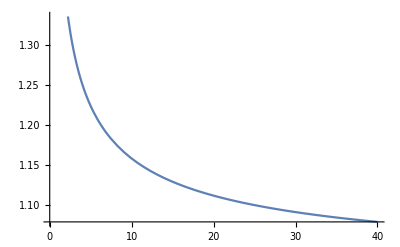

```mathematica
g[0]=Plot[(dK/.parameters[0]),{K,0.1,40}]
```

The curve dq along which the shadow price of capital remains the same from one period to the next, plotted for A=1

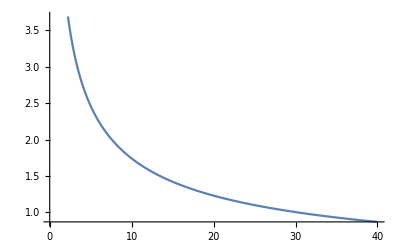

```mathematica
g[1]=Plot[(dq/.parameters[0]),{K,0.1,40}]
```

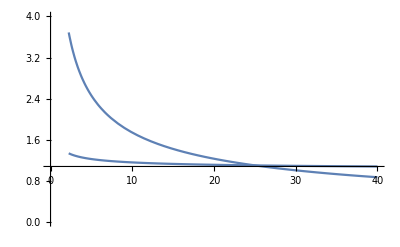

```mathematica
Show[g[0],g[1],PlotRange-> {{0,40},{0,4}}]
```

Because the interval [0,40] is rather large, the figure on which the two curves dK and dq are superposed one over the other is not easy to read. To get a better idea of the relative position of these two curves, we narrow down the range over which K is allowed to vary, say 17≤ K≤ 40.

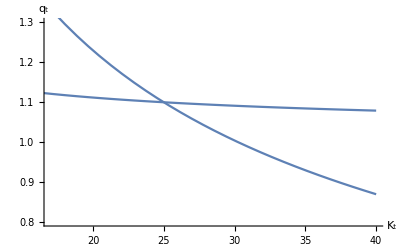

```mathematica
Show[g[0],g[1],PlotRange-> {{17,40},{0.8,1.3}},AxesLabel-> {"K_t","q_t"}]
```

```mathematica
g[2]=Graphics[{AbsolutePointSize[8],Point[{(KBar/.parameters[0]),(qBar/.parameters[0])}]}];
```

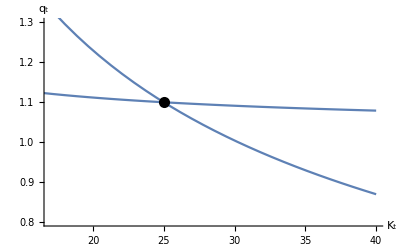

```mathematica
Show[g[0],g[1],g[2],PlotRange-> {{17,40},{0.8,1.3}},AxesLabel-> {"K_t","q_t"}]
```

```mathematica
g[3]=Graphics[Text["TraditionalForm`q",{38,1.07}]];
```

```mathematica
g[4]=Graphics[Text["TraditionalForm`q",{38,0.85}]];
```

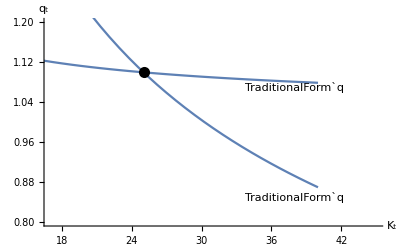

```mathematica
Show[g[0],g[1],g[2],g[3],g[4],PlotRange-> {{17,45},{0.8,1.2}},AxesLabel-> {"K_t","q_t"}]
```

```mathematica
g[5]=Graphics[Arrow[{{18.069397027541758,1.2563736359092752},{20.069397027541758,1.2563736359092752}}]];
```

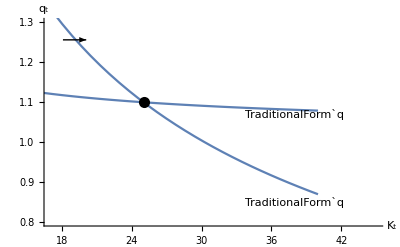

```mathematica
Show[g[0],g[1],g[2],g[3],g[4],g[5],PlotRange-> {{17,45},{0.8,1.3}},AxesLabel-> {"K_t","q_t"}]
```

```mathematica
g[6]=Graphics[Arrow[{{26,1.15},{28.5,1.15}}]];
```

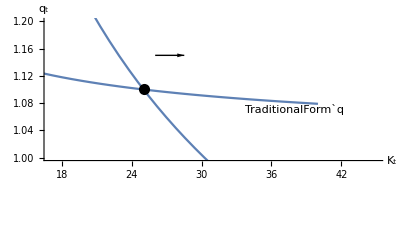

```mathematica
Show[g[0],g[1],g[2],g[3],g[4],g[5],g[6],PlotRange-> {{17,45},{1,1.2}},AxesLabel-> {"K_t","q_t"}]
```

```mathematica
g[7]=Graphics[Arrow[{{26,1.15},{26,1.20}}]];
```

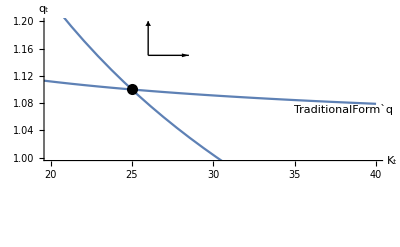

```mathematica
Show[g[0],g[1],g[2],g[3],g[4],g[5],g[6],g[7],PlotRange-> {{20,40},{1,1.2}},AxesLabel-> {"K_t","q_t"}]
```

```mathematica
g[8]=Graphics[Arrow[{{18.069397027541758,1.2563736359092752},{18.069397027541758,1.18}}]];
```

```mathematica
g[9]=Graphics[{AbsolutePointSize[8],Point[{18.069397027541758,1.2563736359092752}]}];
```

```mathematica
g[10]=Graphics[{AbsolutePointSize[8],Point[{26,1.15}]}];
```

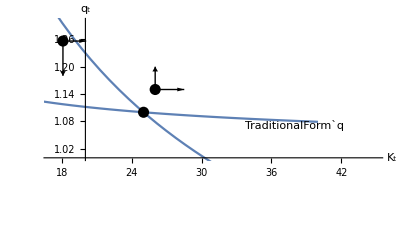

```mathematica
Show[g[0],g[1],g[2],g[3],g[4],g[5],g[6],g[7],g[8],g[9],g[10],PlotRange-> {{17,45},{1,1.3}},AxesOrigin-> {20,1},AxesLabel-> {"K_t","q_t"}]
```

```mathematica
g[11]=Graphics[Text["(K_0^-,q_0^-)",{18,1.27}]];
```

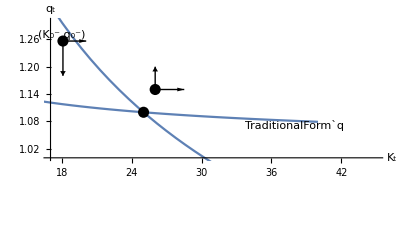

```mathematica
Show[g[0],g[1],g[2],g[3],g[4],g[5],g[6],g[7],g[8],g[9],g[10],g[11],PlotRange-> {{17,45},{1,1.3}},AxesOrigin-> {17,1},AxesLabel-> {"K_t","q_t"}]
```

```mathematica
g[12]=Graphics[Arrow[{{23.5,1.04},{21,1.04}}]];
```

```mathematica
g[13]=Graphics[Arrow[{{23.5,1.04},{23.5,1.0}}]];
```

```mathematica
g[14]=Graphics[{AbsolutePointSize[8],Point[{23.5,1.04}]}];
```

```mathematica
g[15]=Graphics[{AbsolutePointSize[8],Point[{30.5,1.04}]}];
```

```mathematica
g[16]=Graphics[Arrow[{{30.5,1.04},{30.5,1.09}}]];
```

```mathematica
g[17]=Graphics[Arrow[{{30.5,1.04},{28.5,1.04}}]];
```

```mathematica
g[18]=Graphics[{AbsolutePointSize[8],Point[{17,1}]}];
```

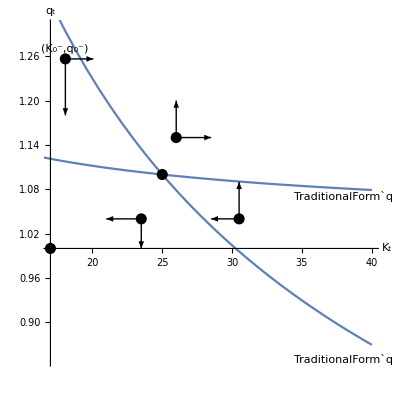

```mathematica
Show[g[0],g[1],g[2],g[3],g[4],g[5],g[6],g[7],g[8],g[9],g[10],g[11],g[12],g[13],g[14],g[15],g[16],g[17],g[18],PlotRange-> {{17,40},{0.85,1.3}},AxesOrigin-> {17,1},AxesLabel-> {"K_t","q_t"},AspectRatio-> 1]
```

```mathematica
g[19]=Graphics[Text["E_0=(K̄,q̄)",{(KBar/.parameters[0])-1,(qBar/.parameters[0])-0.015}]];
```

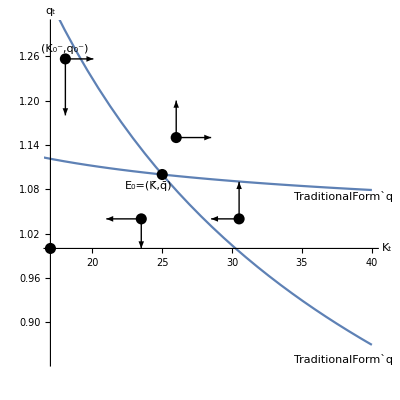

```mathematica
Show[g[0],g[1],g[2],g[3],g[4],g[5],g[6],g[7],g[8],g[9],g[10],g[11],g[12],g[13],g[14],g[15],g[16],g[17],g[18],g[19],PlotRange-> {{17,40},{0.85,1.3}},AxesOrigin-> {17,1},AxesLabel-> {"K_t","q_t"},AspectRatio-> 1]
```

```mathematica
g[20]=Graphics[Text["Region 1",{21.5,1.12}]];
```

```mathematica
g[21]=Graphics[Text["Region 2",{28,1.25}]];
```

```mathematica
g[22]=Graphics[Text["Region 3",{37,1.03}]];
```

```mathematica
g[23]=Graphics[Text["Region 4",{21,1.02}]];
```

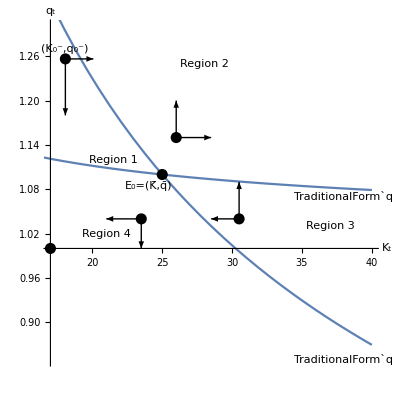

```mathematica
Show[g[0],g[1],g[2],g[3],g[4],g[5],g[6],g[7],g[8],g[9],g[10],g[11],g[12],g[13],g[14],g[15],g[16],g[17],g[18],g[19],g[20],g[21],g[22],g[23],PlotRange-> {{17,40},{0.85,1.3}},AxesOrigin-> {17,1},AxesLabel-> {"K_t","q_t"},AspectRatio-> 1]
```

#### The Backward-Shooting Map: The Case K_0<K̄

The dynamics of the capital stock

```mathematica
eq[1]
```

-K[s]+K[1+s]==(-1+q[1+s]/(1+r))/χ

The dynamics of the shadow price of capital

```mathematica
eq[2]
```

-q[s]+q[1+s]==-A (1+r) α K[s]^(-1+α)+r q[s]

```mathematica
s[2]=Solve[eq[1],K[s]]//Flatten
```

{K[s]→(1+r+χ K[1+s]+r χ K[1+s]-q[1+s])/((1+r) χ)}

```mathematica
eq[2,0]=eq[2]/.s[2]
```

-q[s]+q[1+s]==r q[s]-A (1+r) α ((1+r+χ K[1+s]+r χ K[1+s]-q[1+s])/((1+r) χ))^(-1+α)

```mathematica
s[3]=Solve[eq[2,0],q[s]]//Flatten
```

{q[s]→(-A (1+r) α ((1+r+χ K[1+s]+r χ K[1+s]-q[1+s])/((1+r) χ))^(-1+α)-q[1+s])/(-1-r)}

Let x represent K_(s+1) and y represents q_(s+1). Then (K_s,q_s), as functions of (x,y), represents the image of the backward-shooting map ϕ:(K_(s+1),q_(s+1))→ (K_s,q_s).

```mathematica
s[4]=s[3]/.{K[s+1]-> x,q[s+1]-> y}
```

{q[s]→(-y-A (1+r) α ((1+r-y+x χ+r x χ)/((1+r) χ))^(-1+α))/(-1-r)}

```mathematica
s[4][[1,2]]
```

(-y-A (1+r) α ((1+r-y+x χ+r x χ)/((1+r) χ))^(-1+α))/(-1-r)

```mathematica
s[5]=Solve[eq[1],K[s]]//Flatten
```

{K[s]→(1+r+χ K[1+s]+r χ K[1+s]-q[1+s])/((1+r) χ)}

```mathematica
s[6]=s[5]/.{K[s+1]-> x,q[s+1]-> y}
```

{K[s]→(1+r-y+x χ+r x χ)/((1+r) χ)}

```mathematica
s[6][[1,2]]
```

(1+r-y+x χ+r x χ)/((1+r) χ)

The backward-shooting map ϕ:(a,b)→ ϕ[(a,b)]

```mathematica
ϕ[{a_,b_}]:={s[6][[1,2]]/.parameters[0],s[4][[1,2]]/.parameters[0]}/.{x-> a,y-> b}
```

```mathematica
ϕ[{a,b}]
```

{0.909091 (1.1+1.1 a-b),-0.909091 (-0.576845/(1.1+1.1 a-b)^0.5-b)}

```mathematica
ϕ[{x,y}]
```

{0.909091 (1.1+1.1 x-y),-0.909091 (-0.576845/(1.1+1.1 x-y)^0.5-y)}

```mathematica
KBar
```

(r/(A α))^(1/(-1+α))

```mathematica
parameters[0]
```

{A→1,α→0.5,r→0.1,χ→1}

```mathematica
KBar/.parameters[0]
```

25.

```mathematica
qBar/.parameters[0]
```

1.1

Consider an open ball in the first quadrant of the plane with center (K̄,q̄) and radius 10^-3. Next, choose a point, say (K̄-10^-4,q̄+10^-4) in this open ball as the starting point of the backward-shooting map.

```mathematica
{(KBar/.parameters[0])-10^-4,(qBar/.parameters[0])+10^-4}
```

{24.9999,1.1001}

```mathematica
ϕ[{(KBar/.parameters[0])-10^-4,(qBar/.parameters[0])+10^-4}]
```

{24.9998,1.10009}

```mathematica
ϕ[%]
```

{24.9997,1.10008}

Let us apply the backward-shooting map 560 times.

```mathematica
m[0]=NestList[ϕ,{(KBar/.parameters[0])- 10^-4,(qBar/.parameters[0])+10^-4},560]
```

{{24.9999,1.1001},{24.9998,1.10009},{24.9997,1.10008},{24.9997,1.10008},{24.9996,1.10007},{24.9995,1.10007},{24.9995,1.10006},{24.9994,1.10006},{24.9994,1.10005},{24.9993,1.10005},{24.9993,1.10005},{24.9992,1.10004},{24.9992,1.10004},{24.9991,1.10004},{24.9991,1.10004},{24.9991,1.10004},{24.999,1.10003},{24.999,1.10003},{24.999,1.10003},{24.9989,1.10003},{24.9989,1.10003},{24.9989,1.10003},{24.9989,1.10003},{24.9988,1.10003},{24.9988,1.10003},{24.9988,1.10003},{24.9988,1.10003},{24.9987,1.10003},{24.9987,1.10003},{24.9987,1.10003},{24.9987,1.10003},{24.9986,1.10003},{24.9986,1.10003},{24.9986,1.10003},{24.9985,1.10003},{24.9985,1.10003},{24.9985,1.10003},{24.9985,1.10003},{24.9984,1.10003},{24.9984,1.10003},{24.9984,1.10003},{24.9984,1.10003},{24.9983,1.10003},{24.9983,1.10003},{24.9983,1.10003},{24.9982,1.10003},{24.9982,1.10003},{24.9982,1.10003},{24.9981,1.10004},{24.9981,1.10004},{24.9981,1.10004},{24.998,1.10004},{24.998,1.10004},{24.998,1.10004},{24.9979,1.10004},{24.9979,1.10004},{24.9979,1.10004},{24.9978,1.10004},{24.9978,1.10004},{24.9978,1.10004},{24.9977,1.10004},{24.9977,1.10004},{24.9976,1.10004},{24.9976,1.10005},{24.9976,1.10005},{24.9975,1.10005},{24.9975,1.10005},{24.9974,1.10005},{24.9974,1.10005},{24.9973,1.10005},{24.9973,1.10005},{24.9973,1.10005},{24.9972,1.10005},{24.9972,1.10005},{24.9971,1.10005},{24.9971,1.10006},{24.997,1.10006},{24.997,1.10006},{24.9969,1.10006},{24.9969,1.10006},{24.9968,1.10006},{24.9967,1.10006},{24.9967,1.10006},{24.9966,1.10006},{24.9966,1.10006},{24.9965,1.10007},{24.9965,1.10007},{24.9964,1.10007},{24.9963,1.10007},{24.9963,1.10007},{24.9962,1.10007},{24.9961,1.10007},{24.9961,1.10007},{24.996,1.10008},{24.9959,1.10008},{24.9959,1.10008},{24.9958,1.10008},{24.9957,1.10008},{24.9957,1.10008},{24.9956,1.10008},{24.9955,1.10008},{24.9954,1.10009},{24.9953,1.10009},{24.9953,1.10009},{24.9952,1.10009},{24.9951,1.10009},{24.995,1.10009},{24.9949,1.1001},{24.9949,1.1001},{24.9948,1.1001},{24.9947,1.1001},{24.9946,1.1001},{24.9945,1.1001},{24.9944,1.10011},{24.9943,1.10011},{24.9942,1.10011},{24.9941,1.10011},{24.994,1.10011},{24.9939,1.10011},{24.9938,1.10012},{24.9937,1.10012},{24.9936,1.10012},{24.9935,1.10012},{24.9934,1.10013},{24.9932,1.10013},{24.9931,1.10013},{24.993,1.10013},{24.9929,1.10013},{24.9928,1.10014},{24.9926,1.10014},{24.9925,1.10014},{24.9924,1.10014},{24.9923,1.10015},{24.9921,1.10015},{24.992,1.10015},{24.9919,1.10015},{24.9917,1.10016},{24.9916,1.10016},{24.9914,1.10016},{24.9913,1.10016},{24.9911,1.10017},{24.991,1.10017},{24.9908,1.10017},{24.9907,1.10018},{24.9905,1.10018},{24.9904,1.10018},{24.9902,1.10018},{24.99,1.10019},{24.9898,1.10019},{24.9897,1.10019},{24.9895,1.1002},{24.9893,1.1002},{24.9891,1.1002},{24.9889,1.10021},{24.9888,1.10021},{24.9886,1.10022},{24.9884,1.10022},{24.9882,1.10022},{24.988,1.10023},{24.9878,1.10023},{24.9876,1.10023},{24.9873,1.10024},{24.9871,1.10024},{24.9869,1.10025},{24.9867,1.10025},{24.9864,1.10026},{24.9862,1.10026},{24.986,1.10026},{24.9857,1.10027},{24.9855,1.10027},{24.9852,1.10028},{24.985,1.10028},{24.9847,1.10029},{24.9845,1.10029},{24.9842,1.1003},{24.9839,1.1003},{24.9837,1.10031},{24.9834,1.10031},{24.9831,1.10032},{24.9828,1.10032},{24.9825,1.10033},{24.9822,1.10033},{24.9819,1.10034},{24.9816,1.10035},{24.9813,1.10035},{24.981,1.10036},{24.9806,1.10036},{24.9803,1.10037},{24.98,1.10038},{24.9796,1.10038},{24.9793,1.10039},{24.9789,1.1004},{24.9786,1.1004},{24.9782,1.10041},{24.9778,1.10042},{24.9774,1.10042},{24.9771,1.10043},{24.9767,1.10044},{24.9763,1.10045},{24.9759,1.10045},{24.9754,1.10046},{24.975,1.10047},{24.9746,1.10048},{24.9742,1.10049},{24.9737,1.1005},{24.9733,1.1005},{24.9728,1.10051},{24.9723,1.10052},{24.9719,1.10053},{24.9714,1.10054},{24.9709,1.10055},{24.9704,1.10056},{24.9699,1.10057},{24.9694,1.10058},{24.9689,1.10059},{24.9683,1.1006},{24.9678,1.10061},{24.9672,1.10062},{24.9667,1.10063},{24.9661,1.10064},{24.9655,1.10065},{24.9649,1.10066},{24.9643,1.10067},{24.9637,1.10068},{24.9631,1.1007},{24.9625,1.10071},{24.9618,1.10072},{24.9612,1.10073},{24.9605,1.10074},{24.9598,1.10076},{24.9591,1.10077},{24.9584,1.10078},{24.9577,1.1008},{24.957,1.10081},{24.9563,1.10082},{24.9555,1.10084},{24.9547,1.10085},{24.954,1.10087},{24.9532,1.10088},{24.9524,1.1009},{24.9516,1.10091},{24.9507,1.10093},{24.9499,1.10094},{24.949,1.10096},{24.9482,1.10098},{24.9473,1.10099},{24.9464,1.10101},{24.9454,1.10103},{24.9445,1.10105},{24.9436,1.10106},{24.9426,1.10108},{24.9416,1.1011},{24.9406,1.10112},{24.9396,1.10114},{24.9385,1.10116},{24.9375,1.10118},{24.9364,1.1012},{24.9353,1.10122},{24.9342,1.10124},{24.9331,1.10126},{24.9319,1.10128},{24.9308,1.10131},{24.9296,1.10133},{24.9284,1.10135},{24.9272,1.10137},{24.9259,1.1014},{24.9246,1.10142},{24.9233,1.10145},{24.922,1.10147},{24.9207,1.1015},{24.9193,1.10152},{24.918,1.10155},{24.9165,1.10157},{24.9151,1.1016},{24.9137,1.10163},{24.9122,1.10166},{24.9107,1.10169},{24.9091,1.10171},{24.9076,1.10174},{24.906,1.10177},{24.9044,1.1018},{24.9027,1.10184},{24.9011,1.10187},{24.8994,1.1019},{24.8976,1.10193},{24.8959,1.10197},{24.8941,1.102},{24.8923,1.10203},{24.8904,1.10207},{24.8886,1.1021},{24.8866,1.10214},{24.8847,1.10218},{24.8827,1.10221},{24.8807,1.10225},{24.8787,1.10229},{24.8766,1.10233},{24.8745,1.10237},{24.8723,1.10241},{24.8701,1.10245},{24.8679,1.1025},{24.8656,1.10254},{24.8633,1.10258},{24.861,1.10263},{24.8586,1.10267},{24.8561,1.10272},{24.8537,1.10277},{24.8512,1.10281},{24.8486,1.10286},{24.846,1.10291},{24.8433,1.10296},{24.8407,1.10301},{24.8379,1.10306},{24.8351,1.10312},{24.8323,1.10317},{24.8294,1.10323},{24.8265,1.10328},{24.8235,1.10334},{24.8205,1.10339},{24.8174,1.10345},{24.8142,1.10351},{24.811,1.10357},{24.8078,1.10364},{24.8045,1.1037},{24.8011,1.10376},{24.7977,1.10383},{24.7942,1.10389},{24.7907,1.10396},{24.7871,1.10403},{24.7834,1.1041},{24.7797,1.10417},{24.7759,1.10424},{24.7721,1.10432},{24.7681,1.10439},{24.7641,1.10447},{24.7601,1.10454},{24.756,1.10462},{24.7518,1.1047},{24.7475,1.10478},{24.7431,1.10487},{24.7387,1.10495},{24.7342,1.10504},{24.7296,1.10512},{24.725,1.10521},{24.7202,1.1053},{24.7154,1.1054},{24.7105,1.10549},{24.7055,1.10558},{24.7004,1.10568},{24.6953,1.10578},{24.69,1.10588},{24.6847,1.10598},{24.6792,1.10609},{24.6737,1.10619},{24.6681,1.1063},{24.6623,1.10641},{24.6565,1.10652},{24.6506,1.10663},{24.6446,1.10675},{24.6384,1.10687},{24.6322,1.10699},{24.6258,1.10711},{24.6194,1.10723},{24.6128,1.10736},{24.6061,1.10749},{24.5993,1.10762},{24.5924,1.10775},{24.5853,1.10789},{24.5782,1.10802},{24.5709,1.10816},{24.5634,1.10831},{24.5559,1.10845},{24.5482,1.1086},{24.5404,1.10875},{24.5324,1.1089},{24.5244,1.10906},{24.5161,1.10922},{24.5077,1.10938},{24.4992,1.10954},{24.4905,1.10971},{24.4817,1.10988},{24.4727,1.11005},{24.4636,1.11023},{24.4543,1.11041},{24.4448,1.11059},{24.4352,1.11078},{24.4254,1.11097},{24.4154,1.11116},{24.4053,1.11136},{24.395,1.11156},{24.3845,1.11176},{24.3738,1.11197},{24.3629,1.11218},{24.3518,1.11239},{24.3405,1.11261},{24.3291,1.11284},{24.3174,1.11306},{24.3055,1.11329},{24.2934,1.11353},{24.2811,1.11377},{24.2686,1.11401},{24.2559,1.11426},{24.2429,1.11451},{24.2297,1.11477},{24.2163,1.11503},{24.2026,1.1153},{24.1887,1.11557},{24.1746,1.11585},{24.1602,1.11613},{24.1455,1.11642},{24.1306,1.11671},{24.1154,1.11701},{24.0999,1.11732},{24.0842,1.11762},{24.0681,1.11794},{24.0518,1.11826},{24.0352,1.11859},{24.0183,1.11892},{24.0011,1.11926},{23.9836,1.11961},{23.9658,1.11996},{23.9476,1.12032},{23.9292,1.12068},{23.9104,1.12106},{23.8912,1.12144},{23.8717,1.12182},{23.8519,1.12222},{23.8317,1.12262},{23.8111,1.12303},{23.7902,1.12345},{23.7689,1.12387},{23.7472,1.12431},{23.7251,1.12475},{23.7026,1.1252},{23.6797,1.12566},{23.6564,1.12613},{23.6326,1.1266},{23.6084,1.12709},{23.5838,1.12759},{23.5587,1.12809},{23.5332,1.12861},{23.5072,1.12913},{23.4807,1.12967},{23.4537,1.13022},{23.4262,1.13077},{23.3983,1.13134},{23.3698,1.13192},{23.3408,1.13251},{23.3112,1.13312},{23.2811,1.13373},{23.2504,1.13436},{23.2192,1.135},{23.1874,1.13565},{23.155,1.13632},{23.1219,1.137},{23.0883,1.13769},{23.054,1.1384},{23.0191,1.13912},{22.9836,1.13986},{22.9473,1.14062},{22.9104,1.14138},{22.8728,1.14217},{22.8344,1.14297},{22.7954,1.14379},{22.7556,1.14462},{22.715,1.14547},{22.6737,1.14635},{22.6315,1.14723},{22.5886,1.14814},{22.5448,1.14907},{22.5002,1.15002},{22.4547,1.15099},{22.4084,1.15198},{22.3611,1.15299},{22.313,1.15402},{22.2639,1.15508},{22.2138,1.15616},{22.1627,1.15726},{22.1107,1.15839},{22.0576,1.15954},{22.0035,1.16072},{21.9483,1.16192},{21.892,1.16316},{21.8346,1.16442},{21.776,1.16571},{21.7163,1.16703},{21.6553,1.16838},{21.5932,1.16977},{21.5297,1.17118},{21.465,1.17263},{21.399,1.17412},{21.3316,1.17564},{21.2629,1.17719},{21.1927,1.17879},{21.1211,1.18042},{21.048,1.18209},{20.9733,1.18381},{20.8971,1.18557},{20.8194,1.18737},{20.7399,1.18922},{20.6588,1.19111},{20.576,1.19306},{20.4914,1.19505},{20.405,1.1971},{20.3167,1.1992},{20.2265,1.20136},{20.1344,1.20357},{20.0402,1.20585},{19.944,1.20819},{19.8456,1.21059},{19.7451,1.21306},{19.6423,1.2156},{19.5372,1.21821},{19.4298,1.22089},{19.3199,1.22366},{19.2075,1.2265},{19.0925,1.22943},{18.9748,1.23245},{18.8544,1.23556},{18.7311,1.23876},{18.605,1.24207},{18.4758,1.24548},{18.3436,1.24899},{18.2081,1.25262},{18.0694,1.25637},{17.9272,1.26025},{17.7816,1.26425},{17.6322,1.26839},{17.4792,1.27268},{17.3222,1.27712},{17.1612,1.28171},{16.996,1.28648},{16.8264,1.29141},{16.6524,1.29654},{16.4738,1.30186},{16.2902,1.30739},{16.1017,1.31314},{15.9079,1.31913},{15.7087,1.32536},{15.5039,1.33186},{15.2931,1.33864},{15.0761,1.34571},{14.8528,1.35311},{14.6227,1.36086},{14.3855,1.36897},{14.141,1.37748},{13.8887,1.38642},{13.6283,1.39582},{13.3594,1.40573},{13.0815,1.41618},{12.794,1.42722},{12.4966,1.43891},{12.1885,1.45132},{11.8691,1.46451},{11.5377,1.47858},{11.1936,1.49361},{10.8357,1.50972},{10.4633,1.52705},{10.075,1.54575},{9.6698,1.56602},{9.24615,1.58808},{8.80244,1.61224}}

According to the results obtained after backward-shooting 560 times, if the initial capital stock is K_0^-=8.80244, then the initial shadow price of capital is q_0^-=1.61224, and the system converhes to the long-run equilibrium after 560 periods. For other possible values of K_0^-<K̄, find the element of the list m[0] with the same capital stock value as K_0^-, and the system will converge to the long-run equilibrium from the initial condition (K_0^-,q_0^_).

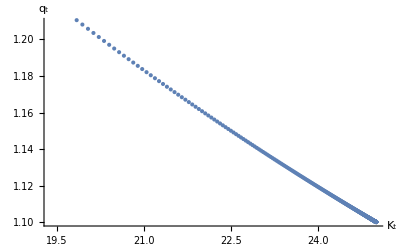

```mathematica
g[24]=ListPlot[m[0],AxesLabel->{""Subscript[K, t],"q_t"}]
```

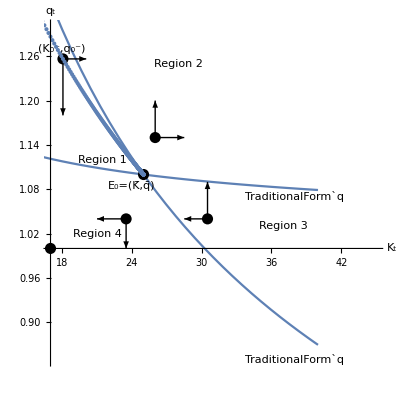

```mathematica
Show[g[0],g[1],g[2],g[3],g[4],g[5],g[6],g[7],g[8],g[9],g[10],g[11],g[12],g[13],g[14],g[15],g[16],g[17],g[18],g[19],g[20],g[21],g[22],g[23],g[24],PlotRange-> {{17,45},{0.85,1.3}},AxesOrigin-> {17,1},AxesLabel-> {"K_t","q_t"},AspectRatio-> 1]
```

#### The Backward-Shooting Map: The Case K_0>K̄

For the case K_0>K̄, choose as the starting point of the backward-shooting map a point in Region 3 that is close to (K̄,q̄).

```mathematica
{(KBar/.parameters[0])+10^-3,(qBar/.parameters[0])-10^-2}
```

{25.001,1.09}

```mathematica
ϕ[{(KBar/.parameters[0])+10^-3,(qBar/.parameters[0])-10^-2}]
```

{25.0101,1.09089}

```mathematica
ϕ[%]
```

{25.0184,1.09168}

Let us apply the backward-shooting  map 560  times.

```mathematica
m[1]=NestList[ϕ,{(KBar/.parameters[0])+ 10^-4,(qBar/.parameters[0])-10^-4},560]
```

{{25.0001,1.0999},{25.0002,1.09991},{25.0003,1.09992},{25.0003,1.09992},{25.0004,1.09993},{25.0005,1.09993},{25.0005,1.09994},{25.0006,1.09994},{25.0006,1.09995},{25.0007,1.09995},{25.0007,1.09995},{25.0008,1.09996},{25.0008,1.09996},{25.0009,1.09996},{25.0009,1.09996},{25.0009,1.09996},{25.001,1.09997},{25.001,1.09997},{25.001,1.09997},{25.0011,1.09997},{25.0011,1.09997},{25.0011,1.09997},{25.0011,1.09997},{25.0012,1.09997},{25.0012,1.09997},{25.0012,1.09997},{25.0012,1.09997},{25.0013,1.09997},{25.0013,1.09997},{25.0013,1.09997},{25.0013,1.09997},{25.0014,1.09997},{25.0014,1.09997},{25.0014,1.09997},{25.0015,1.09997},{25.0015,1.09997},{25.0015,1.09997},{25.0015,1.09997},{25.0016,1.09997},{25.0016,1.09997},{25.0016,1.09997},{25.0016,1.09997},{25.0017,1.09997},{25.0017,1.09997},{25.0017,1.09997},{25.0018,1.09997},{25.0018,1.09997},{25.0018,1.09997},{25.0019,1.09996},{25.0019,1.09996},{25.0019,1.09996},{25.002,1.09996},{25.002,1.09996},{25.002,1.09996},{25.0021,1.09996},{25.0021,1.09996},{25.0021,1.09996},{25.0022,1.09996},{25.0022,1.09996},{25.0022,1.09996},{25.0023,1.09996},{25.0023,1.09996},{25.0024,1.09996},{25.0024,1.09995},{25.0024,1.09995},{25.0025,1.09995},{25.0025,1.09995},{25.0026,1.09995},{25.0026,1.09995},{25.0027,1.09995},{25.0027,1.09995},{25.0027,1.09995},{25.0028,1.09995},{25.0028,1.09995},{25.0029,1.09995},{25.0029,1.09994},{25.003,1.09994},{25.003,1.09994},{25.0031,1.09994},{25.0031,1.09994},{25.0032,1.09994},{25.0033,1.09994},{25.0033,1.09994},{25.0034,1.09994},{25.0034,1.09994},{25.0035,1.09993},{25.0035,1.09993},{25.0036,1.09993},{25.0037,1.09993},{25.0037,1.09993},{25.0038,1.09993},{25.0039,1.09993},{25.0039,1.09993},{25.004,1.09992},{25.0041,1.09992},{25.0041,1.09992},{25.0042,1.09992},{25.0043,1.09992},{25.0043,1.09992},{25.0044,1.09992},{25.0045,1.09992},{25.0046,1.09991},{25.0046,1.09991},{25.0047,1.09991},{25.0048,1.09991},{25.0049,1.09991},{25.005,1.09991},{25.0051,1.0999},{25.0051,1.0999},{25.0052,1.0999},{25.0053,1.0999},{25.0054,1.0999},{25.0055,1.0999},{25.0056,1.09989},{25.0057,1.09989},{25.0058,1.09989},{25.0059,1.09989},{25.006,1.09989},{25.0061,1.09989},{25.0062,1.09988},{25.0063,1.09988},{25.0064,1.09988},{25.0065,1.09988},{25.0066,1.09987},{25.0068,1.09987},{25.0069,1.09987},{25.007,1.09987},{25.0071,1.09987},{25.0072,1.09986},{25.0074,1.09986},{25.0075,1.09986},{25.0076,1.09986},{25.0077,1.09985},{25.0079,1.09985},{25.008,1.09985},{25.0081,1.09985},{25.0083,1.09984},{25.0084,1.09984},{25.0086,1.09984},{25.0087,1.09984},{25.0089,1.09983},{25.009,1.09983},{25.0092,1.09983},{25.0093,1.09982},{25.0095,1.09982},{25.0096,1.09982},{25.0098,1.09982},{25.01,1.09981},{25.0101,1.09981},{25.0103,1.09981},{25.0105,1.0998},{25.0107,1.0998},{25.0109,1.0998},{25.011,1.09979},{25.0112,1.09979},{25.0114,1.09978},{25.0116,1.09978},{25.0118,1.09978},{25.012,1.09977},{25.0122,1.09977},{25.0124,1.09977},{25.0127,1.09976},{25.0129,1.09976},{25.0131,1.09975},{25.0133,1.09975},{25.0135,1.09975},{25.0138,1.09974},{25.014,1.09974},{25.0143,1.09973},{25.0145,1.09973},{25.0147,1.09972},{25.015,1.09972},{25.0153,1.09971},{25.0155,1.09971},{25.0158,1.0997},{25.016,1.0997},{25.0163,1.09969},{25.0166,1.09969},{25.0169,1.09968},{25.0172,1.09968},{25.0175,1.09967},{25.0178,1.09967},{25.0181,1.09966},{25.0184,1.09965},{25.0187,1.09965},{25.019,1.09964},{25.0193,1.09964},{25.0197,1.09963},{25.02,1.09962},{25.0204,1.09962},{25.0207,1.09961},{25.0211,1.0996},{25.0214,1.0996},{25.0218,1.09959},{25.0222,1.09958},{25.0225,1.09958},{25.0229,1.09957},{25.0233,1.09956},{25.0237,1.09955},{25.0241,1.09955},{25.0245,1.09954},{25.0249,1.09953},{25.0254,1.09952},{25.0258,1.09951},{25.0262,1.09951},{25.0267,1.0995},{25.0272,1.09949},{25.0276,1.09948},{25.0281,1.09947},{25.0286,1.09946},{25.0291,1.09945},{25.0296,1.09944},{25.0301,1.09943},{25.0306,1.09942},{25.0311,1.09941},{25.0316,1.0994},{25.0322,1.09939},{25.0327,1.09938},{25.0333,1.09937},{25.0339,1.09936},{25.0344,1.09935},{25.035,1.09934},{25.0356,1.09933},{25.0362,1.09932},{25.0368,1.09931},{25.0375,1.09929},{25.0381,1.09928},{25.0388,1.09927},{25.0394,1.09926},{25.0401,1.09925},{25.0408,1.09923},{25.0415,1.09922},{25.0422,1.09921},{25.0429,1.09919},{25.0437,1.09918},{25.0444,1.09916},{25.0452,1.09915},{25.0459,1.09914},{25.0467,1.09912},{25.0475,1.09911},{25.0483,1.09909},{25.0492,1.09908},{25.05,1.09906},{25.0509,1.09904},{25.0517,1.09903},{25.0526,1.09901},{25.0535,1.09899},{25.0544,1.09898},{25.0554,1.09896},{25.0563,1.09894},{25.0573,1.09892},{25.0582,1.0989},{25.0592,1.09889},{25.0603,1.09887},{25.0613,1.09885},{25.0623,1.09883},{25.0634,1.09881},{25.0645,1.09879},{25.0656,1.09877},{25.0667,1.09875},{25.0678,1.09872},{25.069,1.0987},{25.0702,1.09868},{25.0714,1.09866},{25.0726,1.09864},{25.0738,1.09861},{25.0751,1.09859},{25.0764,1.09856},{25.0777,1.09854},{25.079,1.09851},{25.0804,1.09849},{25.0817,1.09846},{25.0831,1.09844},{25.0846,1.09841},{25.086,1.09838},{25.0875,1.09836},{25.089,1.09833},{25.0905,1.0983},{25.092,1.09827},{25.0936,1.09824},{25.0952,1.09821},{25.0968,1.09818},{25.0985,1.09815},{25.1002,1.09812},{25.1019,1.09809},{25.1036,1.09805},{25.1054,1.09802},{25.1072,1.09799},{25.109,1.09795},{25.1109,1.09792},{25.1128,1.09788},{25.1147,1.09785},{25.1167,1.09781},{25.1186,1.09777},{25.1207,1.09773},{25.1227,1.0977},{25.1248,1.09766},{25.127,1.09762},{25.1291,1.09758},{25.1313,1.09753},{25.1336,1.09749},{25.1358,1.09745},{25.1382,1.09741},{25.1405,1.09736},{25.1429,1.09732},{25.1454,1.09727},{25.1478,1.09723},{25.1504,1.09718},{25.1529,1.09713},{25.1555,1.09708},{25.1582,1.09703},{25.1609,1.09698},{25.1636,1.09693},{25.1664,1.09688},{25.1693,1.09683},{25.1721,1.09677},{25.1751,1.09672},{25.1781,1.09666},{25.1811,1.0966},{25.1842,1.09655},{25.1873,1.09649},{25.1905,1.09643},{25.1938,1.09637},{25.1971,1.09631},{25.2004,1.09624},{25.2038,1.09618},{25.2073,1.09611},{25.2108,1.09605},{25.2144,1.09598},{25.2181,1.09591},{25.2218,1.09584},{25.2256,1.09577},{25.2294,1.0957},{25.2333,1.09563},{25.2373,1.09556},{25.2413,1.09548},{25.2455,1.0954},{25.2496,1.09533},{25.2539,1.09525},{25.2582,1.09517},{25.2626,1.09509},{25.2671,1.095},{25.2716,1.09492},{25.2762,1.09483},{25.2809,1.09474},{25.2857,1.09466},{25.2906,1.09457},{25.2955,1.09447},{25.3005,1.09438},{25.3056,1.09429},{25.3108,1.09419},{25.3161,1.09409},{25.3215,1.09399},{25.3269,1.09389},{25.3325,1.09379},{25.3381,1.09368},{25.3439,1.09358},{25.3497,1.09347},{25.3557,1.09336},{25.3617,1.09325},{25.3678,1.09313},{25.3741,1.09302},{25.3804,1.0929},{25.3869,1.09278},{25.3935,1.09266},{25.4001,1.09254},{25.4069,1.09241},{25.4138,1.09228},{25.4208,1.09215},{25.428,1.09202},{25.4352,1.09189},{25.4426,1.09175},{25.4501,1.09161},{25.4577,1.09147},{25.4655,1.09133},{25.4734,1.09118},{25.4814,1.09104},{25.4895,1.09089},{25.4978,1.09073},{25.5062,1.09058},{25.5148,1.09042},{25.5235,1.09026},{25.5324,1.0901},{25.5414,1.08993},{25.5505,1.08977},{25.5598,1.08959},{25.5693,1.08942},{25.5789,1.08924},{25.5887,1.08907},{25.5986,1.08888},{25.6087,1.0887},{25.619,1.08851},{25.6294,1.08832},{25.6401,1.08813},{25.6508,1.08793},{25.6618,1.08773},{25.673,1.08752},{25.6843,1.08732},{25.6959,1.08711},{25.7076,1.08689},{25.7195,1.08668},{25.7316,1.08646},{25.7439,1.08623},{25.7564,1.086},{25.7692,1.08577},{25.7821,1.08554},{25.7952,1.0853},{25.8086,1.08506},{25.8222,1.08481},{25.836,1.08456},{25.85,1.08431},{25.8643,1.08405},{25.8788,1.08378},{25.8935,1.08352},{25.9085,1.08325},{25.9238,1.08297},{25.9392,1.08269},{25.955,1.08241},{25.971,1.08212},{25.9872,1.08183},{26.0037,1.08153},{26.0205,1.08123},{26.0376,1.08092},{26.0549,1.08061},{26.0726,1.0803},{26.0905,1.07998},{26.1087,1.07965},{26.1272,1.07932},{26.146,1.07898},{26.1651,1.07864},{26.1845,1.0783},{26.2042,1.07794},{26.2243,1.07759},{26.2447,1.07722},{26.2654,1.07686},{26.2864,1.07648},{26.3078,1.0761},{26.3295,1.07572},{26.3516,1.07533},{26.374,1.07493},{26.3968,1.07453},{26.4199,1.07412},{26.4435,1.0737},{26.4674,1.07328},{26.4917,1.07286},{26.5163,1.07242},{26.5414,1.07198},{26.5669,1.07154},{26.5928,1.07108},{26.6191,1.07062},{26.6458,1.07016},{26.6729,1.06968},{26.7005,1.0692},{26.7285,1.06871},{26.7569,1.06822},{26.7858,1.06772},{26.8151,1.06721},{26.8449,1.06669},{26.8752,1.06617},{26.906,1.06564},{26.9372,1.0651},{26.9689,1.06455},{27.0012,1.064},{27.0339,1.06343},{27.0671,1.06286},{27.1009,1.06229},{27.1352,1.0617},{27.17,1.0611},{27.2054,1.0605},{27.2413,1.05989},{27.2777,1.05927},{27.3148,1.05864},{27.3524,1.05801},{27.3905,1.05736},{27.4293,1.05671},{27.4687,1.05604},{27.5086,1.05537},{27.5492,1.05469},{27.5904,1.054},{27.6322,1.0533},{27.6747,1.05259},{27.7178,1.05187},{27.7615,1.05114},{27.8059,1.0504},{27.851,1.04965},{27.8968,1.0489},{27.9433,1.04813},{27.9904,1.04735},{28.0383,1.04657},{28.0868,1.04577},{28.1362,1.04496},{28.1862,1.04414},{28.237,1.04331},{28.2885,1.04248},{28.3408,1.04163},{28.3939,1.04077},{28.4477,1.0399},{28.5023,1.03901},{28.5578,1.03812},{28.614,1.03722},{28.6711,1.03631},{28.729,1.03538},{28.7878,1.03444},{28.8474,1.0335},{28.9078,1.03254},{28.9691,1.03157},{29.0314,1.03059},{29.0945,1.02959},{29.1585,1.02859},{29.2234,1.02757},{29.2892,1.02655},{29.356,1.02551},{29.4237,1.02446},{29.4924,1.02339},{29.562,1.02232},{29.6327,1.02123},{29.7043,1.02013},{29.7769,1.01902},{29.8505,1.0179},{29.9251,1.01676},{30.0008,1.01562},{30.0775,1.01446},{30.1553,1.01329},{30.2341,1.0121},{30.314,1.01091},{30.395,1.0097},{30.4771,1.00848},{30.5603,1.00724},{30.6446,1.006},{30.7301,1.00474},{30.8167,1.00347},{30.9045,1.00219},{30.9934,1.00089},{31.0835,0.999582},{31.1748,0.998261},{31.2673,0.996928},{31.361,0.995583},{31.4559,0.994225},{31.552,0.992854},{31.6495,0.991471},{31.7481,0.990076},{31.848,0.988668},{31.9493,0.987247},{32.0518,0.985815},{32.1556,0.984369},{32.2607,0.982912},{32.3671,0.981442},{32.4749,0.97996},{32.584,0.978465},{32.6945,0.976958},{32.8064,0.975439},{32.9196,0.973908},{33.0342,0.972364},{33.1503,0.970809},{33.2677,0.969242},{33.3866,0.967662},{33.5069,0.966071},{33.6287,0.964468},{33.7519,0.962853},{33.8765,0.961226},{34.0027,0.959588}}

The graph of the backward-shooting  carried  out  560  times

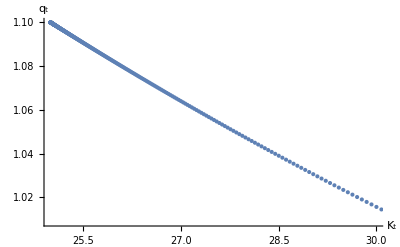

```mathematica
g[25]=ListPlot[m[1],AxesLabel->{""Subscript[K, t],"q_t"}]
```

```mathematica
g[26]=Graphics[{AbsolutePointSize[8],Point[{34.0027022190151,0.9595876713927459}]}];
```

```mathematica
g[27]=Graphics[Text["(K_0^+,q_0^+)",{36.0027022190151,0.945876713927459}]];
```

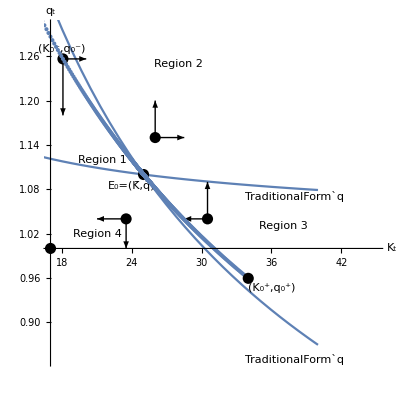

```mathematica
Show[g[0],g[1],g[2],g[3],g[4],g[5],g[6],g[7],g[8],g[9],g[10],g[11],g[12],g[13],g[14],g[15],g[16],g[17],g[18],g[19],g[20],g[21],g[22],g[23],g[24],g[25],g[26],g[27],PlotRange-> {{17,45},{0.85,1.3}},AxesOrigin-> {17,1},AxesLabel-> {"K_t","q_t"},AspectRatio-> 1]
```

### (b) An Unanticipated Rise in Productivity at some time τ>0

Suppose that the system is in steady state, i.e., the system is in state E_0=(K̄,q̄). Suddenly, there is an unanticipated rise in the total factor productivity from A to A+ΔA. If we choose the current period as period 0, the problem faced by the firm is now

(17)	v_0[K̄]=max_((I_t)_(t=0)^∞) ∑_(t=0)^∞ (A+ΔA)F[K_t]-I_t-1/2 χ I_t^2) 

subject to 

(18)	K_(t+1)=K_t+I_t, K_0=K̄.

The solution of the problem constituted by (17) and (18) can be obtained by carrying out the same analysis as in (a), but with A+ΔA in place of A. For the computations carried out by Mathema, we set ΔA=10%.  The value of A is now A+ΔA=1.1.

```mathematica
parameters[1]={A-> 1.1,α-> 0.5,r-> 0.1,χ-> 1}
```

{A→1.1,α→0.5,r→0.1,χ→1}

The curve along which the capital stock does not change from one period to the next

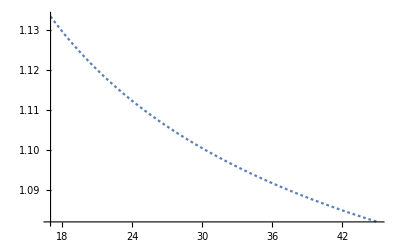

```mathematica
g[28]=Plot[(dK/.parameters[1]),{K,17,45}, PlotStyle -> Dashing[Tiny]]
```

The curve along which the shadow price of capital does not change from one period to the next

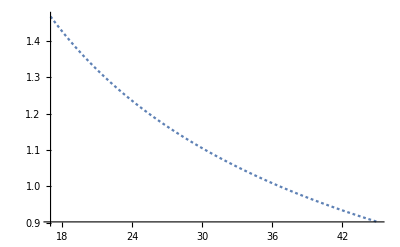

```mathematica
g[29]=Plot[(dq/.parameters[1]),{K,17,45},PlotStyle -> Dashing[Tiny]]
```

```mathematica
KBar
```

(r/(A α))^(1/(-1+α))

```mathematica
KBar/.parameters[1]
```

30.25

```mathematica
g[30]=Graphics[{AbsolutePointSize[8],Point[{(KBar/.parameters[1]),(qBar/.parameters[1])}]}];
```

```mathematica
g[31]=Graphics[Text["(E_1=K̄+ΔK,q̄)",{(KBar/.parameters[1])+2.4,(qBar/.parameters[1])+0.015}]];
```

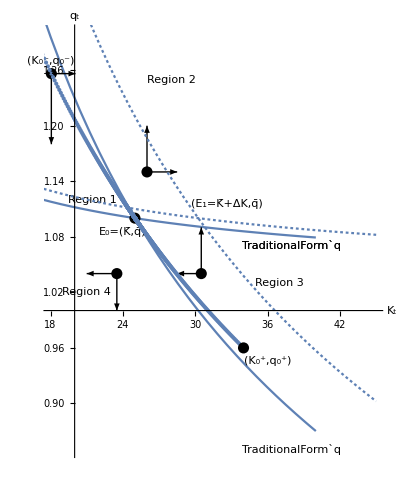

```mathematica
Show[g[0],g[1],g[2],g[3],g[4],g[5],g[6],g[7],g[8],g[9],g[10],g[11],g[12],g[13],g[14],g[15],g[16],g[17],g[18],g[19],g[20],g[21],g[22],g[23],g[24],g[25],g[26],g[27],g[28],g[29],g[3],g[31],PlotRange-> {{18,45},{0.85,1.3}},AxesOrigin-> {20,1},AxesLabel-> {"K_t","q_t"},AspectRatio-> 1.25]
```

```mathematica
g[32]=Graphics[Text["TraditionalForm`q",{40,1.1}]];
```

```mathematica
g[33]=Graphics[Text["TraditionalForm`q",{41,0.97}]];
```

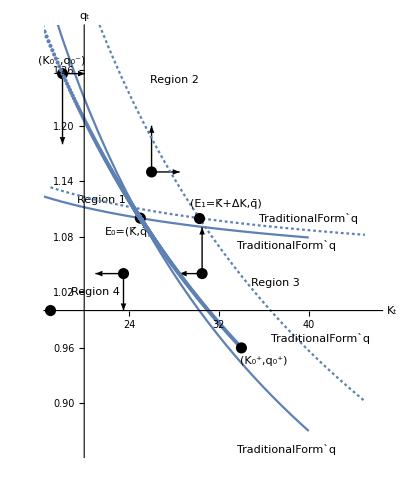

```mathematica
Show[g[0],g[1],g[2],g[3],g[4],g[5],g[6],g[7],g[8],g[9],g[10],g[11],g[12],g[13],g[14],g[15],g[16],g[17],g[18],g[19],g[20],g[21],g[22],g[23],g[24],g[25],g[26],g[27],g[28],g[29],g[30],g[31],g[32],g[33],PlotRange-> {{17,46},{0.85,1.3}},AxesOrigin-> {20,1},AxesLabel-> {"K_t","q_t"},AspectRatio-> 1.25]
```

The backward-shooting map with A+ΔA

```mathematica
ϕ[{a_,b_}]:={s[6][[1,2]]/.parameters[1],s[4][[1,2]]/.parameters[1]}/.{x-> a,y-> b}
```

```mathematica
ϕ[{x,y}]
```

{0.909091 (1.1+1.1 x-y),-0.909091 (-0.634529/(1.1+1.1 x-y)^0.5-y)}

```mathematica
KBar
```

(r/(A α))^(1/(-1+α))

```mathematica
KBar/.parameters[1]
```

30.25

```mathematica
qBar/.parameters[1]
```

1.1

```mathematica
ϕ[{(KBar/.parameters[1])-10^-4,(qBar/.parameters[1])+10^-4}]
```

{30.2498,1.10009}

```mathematica
m[2]=NestList[ϕ,{(KBar/.parameters[1])- 10^-4,(qBar/.parameters[1])+10^-4},660]
```

{{30.2499,1.1001},{30.2498,1.10009},{30.2497,1.10008},{30.2497,1.10008},{30.2496,1.10007},{30.2495,1.10006},{30.2495,1.10006},{30.2494,1.10006},{30.2494,1.10005},{30.2493,1.10005},{30.2493,1.10004},{30.2492,1.10004},{30.2492,1.10004},{30.2491,1.10004},{30.2491,1.10004},{30.2491,1.10003},{30.2491,1.10003},{30.249,1.10003},{30.249,1.10003},{30.249,1.10003},{30.2489,1.10003},{30.2489,1.10003},{30.2489,1.10003},{30.2489,1.10003},{30.2488,1.10003},{30.2488,1.10003},{30.2488,1.10002},{30.2488,1.10002},{30.2488,1.10002},{30.2487,1.10002},{30.2487,1.10002},{30.2487,1.10002},{30.2487,1.10002},{30.2486,1.10002},{30.2486,1.10002},{30.2486,1.10002},{30.2486,1.10002},{30.2486,1.10002},{30.2485,1.10002},{30.2485,1.10003},{30.2485,1.10003},{30.2485,1.10003},{30.2484,1.10003},{30.2484,1.10003},{30.2484,1.10003},{30.2484,1.10003},{30.2483,1.10003},{30.2483,1.10003},{30.2483,1.10003},{30.2483,1.10003},{30.2482,1.10003},{30.2482,1.10003},{30.2482,1.10003},{30.2482,1.10003},{30.2481,1.10003},{30.2481,1.10003},{30.2481,1.10003},{30.2481,1.10003},{30.248,1.10003},{30.248,1.10003},{30.248,1.10003},{30.2479,1.10003},{30.2479,1.10003},{30.2479,1.10003},{30.2479,1.10003},{30.2478,1.10003},{30.2478,1.10004},{30.2478,1.10004},{30.2477,1.10004},{30.2477,1.10004},{30.2477,1.10004},{30.2476,1.10004},{30.2476,1.10004},{30.2476,1.10004},{30.2475,1.10004},{30.2475,1.10004},{30.2475,1.10004},{30.2474,1.10004},{30.2474,1.10004},{30.2473,1.10004},{30.2473,1.10004},{30.2473,1.10004},{30.2472,1.10004},{30.2472,1.10004},{30.2471,1.10005},{30.2471,1.10005},{30.2471,1.10005},{30.247,1.10005},{30.247,1.10005},{30.2469,1.10005},{30.2469,1.10005},{30.2468,1.10005},{30.2468,1.10005},{30.2467,1.10005},{30.2467,1.10005},{30.2466,1.10005},{30.2466,1.10005},{30.2466,1.10005},{30.2465,1.10006},{30.2465,1.10006},{30.2464,1.10006},{30.2463,1.10006},{30.2463,1.10006},{30.2462,1.10006},{30.2462,1.10006},{30.2461,1.10006},{30.2461,1.10006},{30.246,1.10006},{30.246,1.10006},{30.2459,1.10007},{30.2458,1.10007},{30.2458,1.10007},{30.2457,1.10007},{30.2457,1.10007},{30.2456,1.10007},{30.2455,1.10007},{30.2455,1.10007},{30.2454,1.10007},{30.2453,1.10007},{30.2453,1.10008},{30.2452,1.10008},{30.2451,1.10008},{30.2451,1.10008},{30.245,1.10008},{30.2449,1.10008},{30.2448,1.10008},{30.2448,1.10008},{30.2447,1.10008},{30.2446,1.10009},{30.2445,1.10009},{30.2445,1.10009},{30.2444,1.10009},{30.2443,1.10009},{30.2442,1.10009},{30.2441,1.10009},{30.244,1.10009},{30.244,1.1001},{30.2439,1.1001},{30.2438,1.1001},{30.2437,1.1001},{30.2436,1.1001},{30.2435,1.1001},{30.2434,1.1001},{30.2433,1.10011},{30.2432,1.10011},{30.2431,1.10011},{30.243,1.10011},{30.2429,1.10011},{30.2428,1.10011},{30.2427,1.10012},{30.2426,1.10012},{30.2425,1.10012},{30.2424,1.10012},{30.2423,1.10012},{30.2422,1.10012},{30.2421,1.10013},{30.242,1.10013},{30.2418,1.10013},{30.2417,1.10013},{30.2416,1.10013},{30.2415,1.10014},{30.2414,1.10014},{30.2412,1.10014},{30.2411,1.10014},{30.241,1.10014},{30.2408,1.10015},{30.2407,1.10015},{30.2406,1.10015},{30.2404,1.10015},{30.2403,1.10015},{30.2402,1.10016},{30.24,1.10016},{30.2399,1.10016},{30.2397,1.10016},{30.2396,1.10017},{30.2394,1.10017},{30.2393,1.10017},{30.2391,1.10017},{30.239,1.10018},{30.2388,1.10018},{30.2386,1.10018},{30.2385,1.10018},{30.2383,1.10019},{30.2381,1.10019},{30.238,1.10019},{30.2378,1.10019},{30.2376,1.1002},{30.2374,1.1002},{30.2373,1.1002},{30.2371,1.10021},{30.2369,1.10021},{30.2367,1.10021},{30.2365,1.10021},{30.2363,1.10022},{30.2361,1.10022},{30.2359,1.10022},{30.2357,1.10023},{30.2355,1.10023},{30.2353,1.10023},{30.2351,1.10024},{30.2349,1.10024},{30.2346,1.10024},{30.2344,1.10025},{30.2342,1.10025},{30.234,1.10026},{30.2337,1.10026},{30.2335,1.10026},{30.2333,1.10027},{30.233,1.10027},{30.2328,1.10027},{30.2325,1.10028},{30.2323,1.10028},{30.232,1.10029},{30.2318,1.10029},{30.2315,1.10029},{30.2312,1.1003},{30.2309,1.1003},{30.2307,1.10031},{30.2304,1.10031},{30.2301,1.10032},{30.2298,1.10032},{30.2295,1.10033},{30.2292,1.10033},{30.2289,1.10034},{30.2286,1.10034},{30.2283,1.10035},{30.228,1.10035},{30.2277,1.10036},{30.2274,1.10036},{30.227,1.10037},{30.2267,1.10037},{30.2264,1.10038},{30.226,1.10038},{30.2257,1.10039},{30.2253,1.10039},{30.225,1.1004},{30.2246,1.1004},{30.2242,1.10041},{30.2239,1.10042},{30.2235,1.10042},{30.2231,1.10043},{30.2227,1.10043},{30.2223,1.10044},{30.2219,1.10045},{30.2215,1.10045},{30.2211,1.10046},{30.2207,1.10047},{30.2203,1.10047},{30.2198,1.10048},{30.2194,1.10049},{30.2189,1.10049},{30.2185,1.1005},{30.218,1.10051},{30.2176,1.10052},{30.2171,1.10052},{30.2166,1.10053},{30.2162,1.10054},{30.2157,1.10055},{30.2152,1.10055},{30.2147,1.10056},{30.2141,1.10057},{30.2136,1.10058},{30.2131,1.10059},{30.2126,1.1006},{30.212,1.1006},{30.2115,1.10061},{30.2109,1.10062},{30.2104,1.10063},{30.2098,1.10064},{30.2092,1.10065},{30.2086,1.10066},{30.208,1.10067},{30.2074,1.10068},{30.2068,1.10069},{30.2062,1.1007},{30.2055,1.10071},{30.2049,1.10072},{30.2042,1.10073},{30.2036,1.10074},{30.2029,1.10075},{30.2022,1.10076},{30.2015,1.10077},{30.2008,1.10078},{30.2001,1.10079},{30.1994,1.10081},{30.1986,1.10082},{30.1979,1.10083},{30.1971,1.10084},{30.1964,1.10085},{30.1956,1.10087},{30.1948,1.10088},{30.194,1.10089},{30.1932,1.1009},{30.1924,1.10092},{30.1915,1.10093},{30.1907,1.10094},{30.1898,1.10096},{30.189,1.10097},{30.1881,1.10099},{30.1872,1.101},{30.1863,1.10102},{30.1854,1.10103},{30.1844,1.10104},{30.1835,1.10106},{30.1825,1.10108},{30.1815,1.10109},{30.1805,1.10111},{30.1795,1.10112},{30.1785,1.10114},{30.1775,1.10116},{30.1764,1.10117},{30.1754,1.10119},{30.1743,1.10121},{30.1732,1.10122},{30.1721,1.10124},{30.1709,1.10126},{30.1698,1.10128},{30.1686,1.1013},{30.1675,1.10132},{30.1663,1.10133},{30.165,1.10135},{30.1638,1.10137},{30.1626,1.10139},{30.1613,1.10141},{30.16,1.10143},{30.1587,1.10146},{30.1574,1.10148},{30.156,1.1015},{30.1547,1.10152},{30.1533,1.10154},{30.1519,1.10156},{30.1505,1.10159},{30.149,1.10161},{30.1476,1.10163},{30.1461,1.10166},{30.1446,1.10168},{30.143,1.10171},{30.1415,1.10173},{30.1399,1.10176},{30.1383,1.10178},{30.1367,1.10181},{30.1351,1.10183},{30.1334,1.10186},{30.1317,1.10189},{30.13,1.10191},{30.1283,1.10194},{30.1265,1.10197},{30.1247,1.102},{30.1229,1.10203},{30.121,1.10206},{30.1192,1.10209},{30.1173,1.10212},{30.1153,1.10215},{30.1134,1.10218},{30.1114,1.10221},{30.1094,1.10224},{30.1074,1.10228},{30.1053,1.10231},{30.1032,1.10234},{30.1011,1.10238},{30.0989,1.10241},{30.0967,1.10245},{30.0945,1.10248},{30.0922,1.10252},{30.0899,1.10256},{30.0876,1.10259},{30.0853,1.10263},{30.0829,1.10267},{30.0804,1.10271},{30.078,1.10275},{30.0755,1.10279},{30.073,1.10283},{30.0704,1.10287},{30.0678,1.10291},{30.0651,1.10295},{30.0624,1.103},{30.0597,1.10304},{30.057,1.10308},{30.0542,1.10313},{30.0513,1.10317},{30.0484,1.10322},{30.0455,1.10327},{30.0425,1.10332},{30.0395,1.10336},{30.0365,1.10341},{30.0334,1.10346},{30.0302,1.10351},{30.027,1.10356},{30.0238,1.10362},{30.0205,1.10367},{30.0171,1.10372},{30.0138,1.10378},{30.0103,1.10383},{30.0068,1.10389},{30.0033,1.10394},{29.9997,1.104},{29.9961,1.10406},{29.9924,1.10412},{29.9886,1.10418},{29.9848,1.10424},{29.981,1.1043},{29.9771,1.10437},{29.9731,1.10443},{29.9691,1.1045},{29.965,1.10456},{29.9608,1.10463},{29.9566,1.1047},{29.9524,1.10476},{29.948,1.10483},{29.9436,1.1049},{29.9392,1.10498},{29.9347,1.10505},{29.9301,1.10512},{29.9254,1.1052},{29.9207,1.10527},{29.9159,1.10535},{29.911,1.10543},{29.9061,1.10551},{29.9011,1.10559},{29.896,1.10567},{29.8908,1.10576},{29.8856,1.10584},{29.8803,1.10593},{29.8749,1.10601},{29.8694,1.1061},{29.8639,1.10619},{29.8583,1.10628},{29.8526,1.10637},{29.8468,1.10647},{29.8409,1.10656},{29.8349,1.10666},{29.8289,1.10676},{29.8227,1.10686},{29.8165,1.10696},{29.8102,1.10706},{29.8037,1.10717},{29.7972,1.10727},{29.7906,1.10738},{29.7839,1.10749},{29.7771,1.1076},{29.7702,1.10771},{29.7632,1.10782},{29.7561,1.10794},{29.7489,1.10806},{29.7415,1.10817},{29.7341,1.10829},{29.7266,1.10842},{29.7189,1.10854},{29.7111,1.10867},{29.7033,1.1088},{29.6953,1.10893},{29.6872,1.10906},{29.6789,1.10919},{29.6706,1.10933},{29.6621,1.10947},{29.6535,1.10961},{29.6447,1.10975},{29.6359,1.10989},{29.6269,1.11004},{29.6178,1.11019},{29.6085,1.11034},{29.5991,1.11049},{29.5896,1.11065},{29.5799,1.11081},{29.5701,1.11097},{29.5601,1.11113},{29.55,1.1113},{29.5397,1.11147},{29.5293,1.11164},{29.5187,1.11181},{29.508,1.11199},{29.4971,1.11216},{29.486,1.11235},{29.4748,1.11253},{29.4634,1.11272},{29.4518,1.11291},{29.4401,1.1131},{29.4282,1.1133},{29.4161,1.11349},{29.4038,1.1137},{29.3914,1.1139},{29.3787,1.11411},{29.3659,1.11432},{29.3529,1.11454},{29.3397,1.11475},{29.3263,1.11498},{29.3127,1.1152},{29.2988,1.11543},{29.2848,1.11566},{29.2706,1.1159},{29.2561,1.11614},{29.2415,1.11638},{29.2266,1.11663},{29.2114,1.11688},{29.1961,1.11713},{29.1805,1.11739},{29.1647,1.11765},{29.1487,1.11792},{29.1324,1.11819},{29.1158,1.11847},{29.0991,1.11875},{29.082,1.11903},{29.0647,1.11932},{29.0472,1.11961},{29.0293,1.11991},{29.0112,1.12021},{28.9929,1.12052},{28.9742,1.12083},{28.9553,1.12115},{28.936,1.12147},{28.9165,1.1218},{28.8967,1.12213},{28.8766,1.12247},{28.8561,1.12282},{28.8354,1.12316},{28.8143,1.12352},{28.793,1.12388},{28.7713,1.12425},{28.7492,1.12462},{28.7268,1.125},{28.7041,1.12538},{28.681,1.12577},{28.6576,1.12617},{28.6338,1.12658},{28.6096,1.12699},{28.5851,1.1274},{28.5602,1.12783},{28.5349,1.12826},{28.5092,1.1287},{28.4831,1.12915},{28.4566,1.1296},{28.4297,1.13006},{28.4024,1.13053},{28.3746,1.131},{28.3465,1.13149},{28.3178,1.13198},{28.2887,1.13248},{28.2592,1.13299},{28.2292,1.13351},{28.1988,1.13404},{28.1678,1.13457},{28.1364,1.13512},{28.1045,1.13567},{28.072,1.13624},{28.0391,1.13681},{28.0056,1.13739},{27.9716,1.13799},{27.9371,1.13859},{27.902,1.1392},{27.8664,1.13983},{27.8302,1.14047},{27.7934,1.14111},{27.756,1.14177},{27.718,1.14244},{27.6795,1.14312},{27.6402,1.14382},{27.6004,1.14452},{27.5599,1.14524},{27.5188,1.14598},{27.477,1.14672},{27.4345,1.14748},{27.3914,1.14825},{27.3475,1.14904},{27.3029,1.14984},{27.2576,1.15065},{27.2116,1.15148},{27.1648,1.15233},{27.1172,1.15319},{27.0688,1.15407},{27.0197,1.15496},{26.9697,1.15587},{26.9189,1.1568},{26.8673,1.15775},{26.8148,1.15871},{26.7614,1.15969},{26.7072,1.16069},{26.652,1.16171},{26.5959,1.16275},{26.5388,1.16381},{26.4808,1.16489},{26.4219,1.16599},{26.3619,1.16711},{26.3009,1.16825},{26.2388,1.16942},{26.1757,1.17061},{26.1115,1.17182},{26.0462,1.17306},{25.9798,1.17433},{25.9122,1.17562},{25.8435,1.17693},{25.7735,1.17827},{25.7024,1.17965},{25.63,1.18104},{25.5563,1.18247},{25.4813,1.18393},{25.405,1.18542},{25.3274,1.18694},{25.2483,1.1885},{25.1679,1.19008},{25.086,1.19171},{25.0026,1.19336},{24.9177,1.19506},{24.8313,1.19679},{24.7433,1.19856},{24.6537,1.20037},{24.5625,1.20222},{24.4696,1.20411},{24.3749,1.20605},{24.2785,1.20803},{24.1803,1.21006},{24.0802,1.21213},{23.9783,1.21426},{23.8744,1.21644},{23.7686,1.21866},{23.6607,1.22095},{23.5508,1.22329},{23.4387,1.22568},{23.3244,1.22814},{23.2079,1.23066},{23.0892,1.23324},{22.968,1.23589},{22.8445,1.23861},{22.7185,1.2414},{22.5899,1.24427},{22.4588,1.24721},{22.325,1.25023},{22.1884,1.25333},{22.049,1.25652},{21.9067,1.2598},{21.7614,1.26318},{21.6131,1.26665},{21.4616,1.27022},{21.3068,1.2739},{21.1487,1.27769},{20.9872,1.28159},{20.8221,1.28561},{20.6534,1.28976},{20.4809,1.29404},{20.3045,1.29846},{20.1241,1.30302},{19.9395,1.30774},{19.7506,1.31261},{19.5574,1.31765},{19.3595,1.32286},{19.1569,1.32826},{18.9494,1.33386},{18.7368,1.33966},{18.5189,1.34568},{18.2956,1.35193},{18.0665,1.35843},{17.8316,1.36518},{17.5905,1.37221},{17.3431,1.37953},{17.0889,1.38717},{16.8279,1.39514},{16.5596,1.40346},{16.2837,1.41217},{15.9999,1.42129},{15.7078,1.43086},{15.407,1.4409},{15.0971,1.45146}}

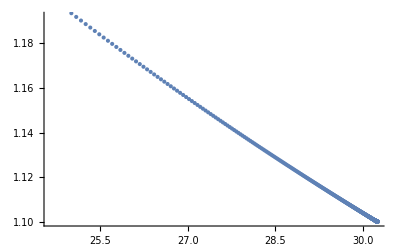

```mathematica
g[34]=ListPlot[m[2]]
```

```mathematica
g[35]=Graphics[{AbsolutePointSize[8],Point[{25.00261624411896,1.1933630218897364}]}];
```

```mathematica
g[36]=Graphics[Text["(K̄,q̄+Δq)",{25,1.21}]];
```

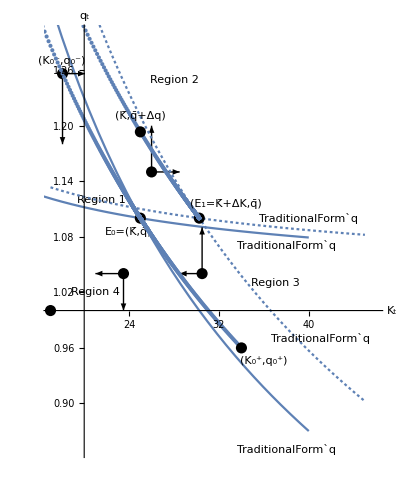

```mathematica
Show[g[0],g[1],g[2],g[3],g[4],g[5],g[6],g[7],g[8],g[9],g[10],g[11],g[12],g[13],g[14],g[15],g[16],g[17],g[18],g[19],g[20],g[21],g[22],g[23],g[24],g[25],g[26],g[27],g[28],g[29],g[30],g[31],g[32],g[33],g[34],g[35],g[36],PlotRange-> {{17,46},{0.85,1.3}},AxesOrigin-> {20,1},AxesLabel-> {"K_t","q_t"},AspectRatio-> 1.25]
```

2.  In this exercise, we study the consumption and investment decisions made by the residents of a small open economy. The approach adopted is that of the representative agent; that is, the consumption and investment decisions made by all the economic agents - consumers and firms - can be thought of as the outcomes of the utility maximization of a representative agent who lives forever. In the exercise, time is discrete and denoted by t,t=0,1,...
   
Suppose that the small open economy - often called the home economy - begins at date t=0 with B_0 as the amount of foreign assets and K_0 as the capital stock it owns. The home economy faces a constant world interest rate r at each date t,t=0,1,... 

Let B_t be the stock of foreign assets that the home economy owns at the beginning of period t. The interest income earned at the end of period t is thus equal to r B_t. Another source of income for the home economy comes from its production activities. The output, at the end of period t, of the home economy is assumed to be given by Y_t=A_t F[K_t], where A_t is the total factor productivity in period t and  K_t is the capital stock available at the beginning of that period. We shall assume that F[0]=0,F'[K]>0,F''[K]<0, lim_(K→ 0) F'[K]=∞, lim_(K→ ∞) F'[K]=0. 

At the end of period t, the total income before tax is thus given by Y_t+r B_t. Let G_t denote the amount of government expenditures, made at the end of period t. We suppose that G_t is obtained by taxing the residents of the home economy. The disposable income of the  domestic residents, at the end of period t, is thus r B_t+Y_t-G_t, which must be allocated between current consumption, say C_t, and  investment, say I_t.

In the balance of payments, compiled at the end of period t, the current account is given by
(1)	CA_t=B_(t+1)-B_t=r B_t+Y_t-G_t-I_t-C_t.

The utility obtained by the representative agent at the end of period t is assumed to be given by u[C_t], with u'[C][>0,u''[C]<0. The representative agent is supposed to discount her utility, using β,0<β<1, as the discount factor. As for the capital stock, its dynamics is governed by the following difference equation:

(2)	K_(t+1)=K_t+I_t.

The problem of the representative agent can be stated formally as follows:
(3)	v_0[B_0,K_0]=max_((C_t,I_t)_(t=0)^∞) ∑_(t=0)^∞ β^t u[C_t)]

subject to the following dynamic equations:

(4)	B_(t+1)=(1+r) B_t+A_t F[K_t]-G_t-I_t-C_t,
(5)	K_(t+1)=K_t+I_t,

and the no Ponzi game costraint
(6)	lim_(t→ ∞) (1/(1+r))^t B_t=0,

where B_0 and K_0 are given. Note that v_0[B_0,K_0] represents the optimal present value of the stream of utilities of the representative agent, given that she begins period 0 with B_0 as her stock of foreign bonds and K_0 as the stock of capital she owns.

(a) How do you determine the optimal consumption and the optimal investment in each period?
(b) Suppose that A_t=A=constant, t=0,1,... Also, suppose that the utility function is u[C]=Log[C].  Compute the current account in a period, say t, and explain under what condition the small open economy runs a current account deficit, a current account surplus, and a balanced current account.

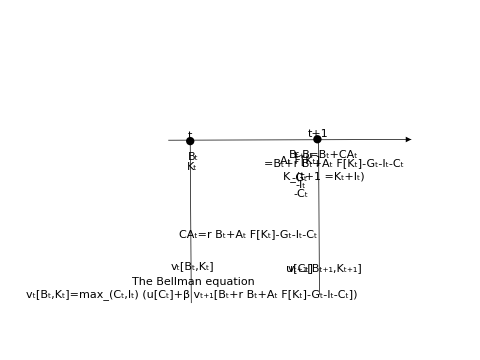
Suppose that the representative individual begins period t with B_t as the stock of foreign bonds she holds and K_t as the stock of capital she owns. The Bellman equation for her utility maximization problem is:

(1)	v_t[B_t,K_t]=max_(C_t,I_t) (u[C_t]+β v_(t+1)[(1+r) B_t+A_t F[K_t]-G_t-I_t-C_t,K_t+I_t]).
-Graphics-
The first-order condition that characterizes the optimal consumption in period t is

(2)	∂/(∂C_t)(u[C_t]+β v_(t+1)[(1+r) B_t+A_t F[K_t]-G_t-I_t-C_t,K_t+I_t])
	=u'[C_t]-β (∂v_(t+1)[(1+r) B_t+A_t F[K_t]-G_t-I_t-C_t,K_t+I_t])/(∂ B_(t+1))=0,
The first-order condition that characterizes the optimal investment in period t is

(3)	∂/(∂I_t)(u[C_t]+β v_(t+1)[(1+r) B_t+A_t F[K_t]-G_t-I_t-C_t,K_t+I_t])
	=-(∂v_(t+1)[(1+r) B_t+A_t F[K_t]-G_t-I_t-C_t,K_t+I_t])/(∂ B_(t+1))
		+(∂v_(t+1)[(1+r) B_t+A_t F[K_t]-G_t-I_t-C_t,K_t+I_t])/(∂ K_(t+1))=0.

Applying the envelope theorem at date t, we obtain

(4)	(∂v_t[B_t,K_t])/(∂B_t)=(∂(u[C_t]+β v_(t+1)[(1+r) B_t+A_t F[K_t]-G_t-I_t-C_t,K_t+I_t]))/(∂B_t)|_(C_t=C_t^*,I_t=I_t^*)
		=(1+r)β(∂v_(t+1)[ B_(t+1),K_(t+1)])/(∂ B_(t+1)),
(5)	(∂v_t(B_t,K_t))/(∂K_t)=(∂(u[C_t]+β v_(t+1)[(1+r) B_t+A_t F[K_t]-G_t-I_t-C_t,K_t+I_t]))/(∂K_t)|_(C_t=C_t^*,I_t=I_t^*)
		=β((∂v_(t+1)[ B_(t+1),K_(t+1)])/(∂ B_(t+1))A_t F'[K_t]+(∂v_(t+1)[ B_(t+1),K_(t+1)])/(∂ K_(t+1))).

Let us rewrite (2) as

(6)	u'[C_t]=β (∂v_(t+1)[B_(t+1),K_(t+1)])/(∂ B_(t+1))

and (3) as

(7)	(∂v_(t+1)[B_(t+1),K_(t+1)])/(∂ B_(t+1))=(∂v_(t+1)[B_(t+1),K_(t+1)])/(∂ K_(t+1)).

Now forwarding (4) one period, we obtain

(8)	(∂v_(t+1)[B_(t+1),K_(t+1)])/(∂B_(t+1))=(1+r)β(∂v_(t+2)[B_(t+2),K_(t+2)])/(∂ B_(t+2)).

Forwarding (6) one period, we obtain

(9)	u'[C_(t+1)]=β (∂v_(t+2)[B_(t+2),K_(t+2)])/(∂ B_(t+2))
	                    =((1+r)β)/(1+r)(∂v_(t+2)[B_(t+2),K_(t+2)])/(∂ B_(t+2))
	                                     =1/(1+r)(∂v_(t+1)[B_(t+1),K_(t+1)])/(∂B_(t+1))
				  =1/(1+r)u'[C_t]/β.

Note that the equality on the third line of (9) has been obtained with the help of (8), and the equality on the last line of (9) with the help of (6). We have just established

(10)	(1+r)β u'[C_(t+1)]=u'[C_t].

It follows from the strict concavity of the utility function that C_(t+1)>C_t   >if (1+r)  β>1, and vice versa. Only in the case (1+r)β=1 is consumption constant over time. There is no stationary equilibrium unless β(1+r)=1.

Forwarding (4) and (5) one period, we obtain

(11)	(∂v_(t+1)[B_(t+1),K_(t+1)])/(∂B_(t+1))=(1+r)β(∂v_(t+2)[B_(t+2),K_(t+2)])/(∂ B_(t+2)).

(12)	(∂v_(t+1)(B_(t+1),K_(t+1)))/(∂K_(t+1))=β((∂v_(t+2)[ B_(t+2),K_(t+2)])/(∂ B_(t+2))A_(t+1)F'[K_(t+1)]+(∂v_(t+2)[ B_(t+2),K_(t+2)])/(∂ K_(t+2)))
		=β(∂v_(t+2)[B_(t+2),K_(t+2)])/(∂ B_(t+2))(1+A_(t+1)F'[K_(t+1)]).

Note that the last line in (12) has been obtained with the help of (7) - forwarded one period. Again using (7), we can equate (11) and (12) to obtain

	(1+r)β(∂v_(t+2)[B_(t+2),K_(t+2)])/(∂ B_(t+2))=β(∂v_(t+2)[B_(t+2),K_(t+2)])/(∂ B_(t+2))(1+A_(t+1)F'[K_(t+1)]),
i.e.,

(13)	A_(t+1)F'(K_(t+1))=r.

Note that (13) allows us to compute K_(t+1), say
(14)	K_(t+1)=(F')^-1[r/(A_(t+1))],
from which the optimal investment in period t can be determined by
(15)	I_t^*=K_(t+1)-K_t=(F')^-1[r/(A_(t+1))]-K_t.

Now suppose that the utility function has the following form:
	u[C]=C^(1-1/σ)/(1-1/σ). 
Then we have 
	u'[C]=C^(-1/σ).

Using the preceding result in (10), we obtain

(16)	(1+r)(β(C_(t+1)))^(-1/σ)=(C_t)^(-1/σ)⟹C_(t+1)=((1+r)β)^σ C_t.

The discounted value of the stream of expenditures (C_s^*,I_s^*),s≥ t, discounted to time t, is

(17)	∑_(s=t)^∞ (1/(1+r))^(s-t)(C_s^*+I_s^*), 

and the discounted value - discounted to the end of period t - is
(18)	(1+r) B_t+∑_(s=t)^∞ (1/(1+r))^(s-t)(Y_s-G_s).

Note that in (18) the term (1+r) B_t represents the value of the foreign assets (the original foreign bonds B_t plus the interest r B_t earned by B_t. As for the expression ∑_(s=t)^∞ (1/(1+r))^(s-t)(Y_s-G_s), note that Y_s is the value of income from production (earned from the oiwnership of capital K_t), while G_s is the tax collected by the State for public consumption. The difference (Y_s-G_s) thus represents the income obtained from production activities net of taxes. The no-Ponzi game condition implies that the discounted value of expenditures must be equal to the discounted value of wealth:

(19)	∑_(s=t)^∞ (1/(1+r))^(s-t)(C_s^*+I_s^*)=(1+r) B_t+∑_(s=t)^∞ (1/(1+r))^(s-t)(Y_s-G_s), 
which can be rewritten as
 	
(20)	∑_(s=t)^∞ (1/(1+r))^(s-t)C_s^*=(1+r) B_t+∑_(s=t)^∞ (1/(1+r))^(s-t)(Y_s-G_s-I_s^*). 
  
Now according to (16), we have

(21)	C_(t+1)=((1+r)β)^σ C_t,
C_(t+2)=((1+r)β)^σ C_(t+1)=((1+r)β)^σ((1+r)β)^σ C_t,
...
C_s=((1+r)β)^σ c_(s-1)=(((1+r)β)^σ)^(s-t)C_t,
..

Thus, we have

(20)	∑_(s=t)^∞ (1/(1+r))^(s-t)C_s^*=∑_(s=t)^∞ (1/(1+r))^(s-t)(((1+r)β)^σ)^(s-t)C_t^*
		=∑_(s=t)^∞ (((1+r)β)^σ/(1+r))^(s-t)C_t^*=(1+r) B_t+∑_(s=t)^∞ (1/(1+r))^(s-t)(Y_s-G_s-I_s^*). 
  
Assuming that ((1+r)β)^σ<1, we can simplify the last equality in (20) as

(21)	1/(1-((1+r)β)^σ/(1+r))C_t^*=(1+r) B_t+∑_(s=t)^∞ (1/(1+r))^(s-t)(Y_s-G_s-I_s^*).
or
(22)	(1+r)/(1+r-((1+r)β)^σ)C_t^*=(1+r )B_t+∑_(s=t)^∞ (1/(1+r))^(s-t)(Y_s-G_s-I_s^*).

The consumption in period t is then given by

(23)	C_t^*=(1+r-((1+r)β)^σ)/(1+r)((1+r )B_t+∑_(s=t)^∞ (1/(1+r))^(s-t)(Y_s-G_s-I_s^*)).

Using (23) in the current account, we obtain

(24)	CA_t=r B_t+Y_t-G_t-I_t^*-C_t^*
	=r B_t+Y_t-G_t-I_t^*-(1+r-((1+r)β)^σ)/(1+r)((1+r )B_t+∑_(s=t)^∞ (1/(1+r))^(s-t)(Y_s-G_s-I_s^*))
		=r B_t+Y_t-G_t-I_t^*-r/(1+r)((1+r )B_t+∑_(s=t)^∞ (1/(1+r))^(s-t)(Y_s-G_s-I_s^*))
			-(1-((1+r)β)^σ)/(1+r)((1+r )B_t+∑_(s=t)^∞ (1/(1+r))^(s-t)(Y_s-G_s-I_s^*)).

Now suppose that for all s≥ t, Y_s=Ȳ=constant, G_s=Ḡ=constant, I_s^*=Ī=constnat. Under these assumptions, (24) takes on the following form:

(25)	CA_t=r B_t+Y_t-G_t-I_t^*-r/(1+r)((1+r )B_t+(1+r)/r Ȳ-(1+r)/r Ḡ-(1+r)/r Ī)
		-(1-((1+r)β)^σ)/(1+r)((1+r )B_t+∑_(s=t)^∞ (1/(1+r))^(s-t)(Y_s-G_s-I_s^*))
	=(Y_t-Ȳ)+(G_t-Ḡ)+(I_t^*-Ī)
		-(1-((1+r)β)^σ)/(1+r)((1+r )B_t+∑_(s=t)^∞ (1/(1+r))^(s-t)(Y_s-G_s-I_s^*))
	=-(1-((1+r)β)^σ)/(1+r)((1+r )B_t+∑_(s=t)^∞ (1/(1+r))^(s-t)(Y_s-G_s-I_s^*)).

Furthermore, if β(1+r)<1, i.e., if the representative individual is impatient, then

(26)	CA_t=-((1+r )B_t+∑_(s=t)^∞ (1/(1+r))^(s-t)(Y_s-G_s-I_s))<0, 

which means that the home economy will run a negative current account. On the other hand, if β(1+r)>1, then it will run a surplus current account. Only when β(1+r)=1 is the current account in balance.

3.  Consider an individual, assumed to live forever, whose wealth in period 0 is ω_0>0. This individual does not work and his consumption in each period t=0,1,... is financed from his wealth. 

Let c_0 denote his consumption in period 0. The amount of wealth left after paying for the consumption in period 0 is thus ω_0-c_0, which is then invested. At the beginning of period 1, the wealth of this individual is given by ω_1=r_1(ω_0-c_0), where r_1 is the rate of return to the investment made in period 0. Assume that r_1 is random and that the uncertainty concerning r_1 is resolved at the beginning of period 1. In period 1, the individual has to choose a consumption level c_1. The wealth of the individual at the beginning of period 2 is then  ω_2=r_2(ω_1-c_1), where r_2 is the random rate of return to the investment made in period 1. In general, if ω_t is the wealth of the individual at the beginning of period t, and c_t is his consumption in that period, then the wealth at his disposal at the beginning of period t+1 is  ω_(t+1)=r_(t+1)(ω_t-c_t), where r_(t+1) is the rate of return to the investment made in period t. Assume that r_t,t=0,1,2,..., are independent and identically distributed random variables. 

Find a consumption function , say c_t=c[x_t], that gives the consumption in each period as a function of the wealth available at the beginning of that period, to maximize the following expected discounted utility: E[∑_(t=0)^∞ δ^t 1/(1-γ)c_t^(1-γ)], where E denote the expectation operator and δ,0<δ<1, is the factor of discount. In answering this question, assume E[r_t]=r̄<1/δ-1.